-Graphics-

# Quantum interference

## Attenuators in both the arms of Mach-Zehnder

## Setup

#### Visibility

```mathematica
Vis[xmax_,xmin_]:=N[(xmax-xmin)/(xmax+xmin)];
```

#### Truncated TMSV Normalization

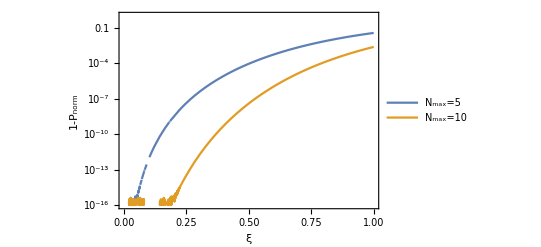

```mathematica
Prob[ξ_,n_]:=(1/Cosh[ξ])^2(1-(Tanh[ξ])^(2(n+1)))/(1-(Tanh[ξ])^2);
LogPlot[{1-Prob[ξ,5],1-Prob[ξ,10]},{ξ,0,1.0},Frame->True,FrameLabel->{"ξ","1-P_norm","Normalization Error vs. Squeezing"},PlotLegends->{"N_max=5","N_max=10"},LabelStyle->Large]
```

#### Single Beam splitter transformation

```mathematica
B[θ_,ϕ_,a_,b_,N_]:=Table[Boole[i==j]*Cos[θ]^Boole[i==a ||i==b]+I Sin[θ]*( E^(I ϕ)Boole[i==a&&j==b]+E^(-I ϕ)Boole[i==b&&j==a]),{i,N},{j,N}];
```

#### Phase shift transformation

```mathematica
R[ϕ_,a_,N_]:=Table[Boole[i==j]*E^(I ϕ*Boole[i==a]),{i,N},{j,N}];
```

#### Creation operator, photon number basis

```mathematica
CR[N_]:=Table[Boole[i==j+1]*Sqrt[i-1],{i,N},{j,N}];
ID[N_]:=IdentityMatrix[N];
```

#### RULES for (esc c* esc) symbol

```mathematica
(* https://mathematica.stackexchange.com/questions/216684/calculate-dot-product-of-two-tensor-products-in-mathematica-as-tensorproduct *)
ClearAll[CircleTimes];
(* "Ordinary multiplication" --- commutative, required for calculating terms like (a3)(a4)  *)
CircleTimes/:(a1_⊗b1_⊗c1_⊗d1_)(a2_⊗b2_⊗c2_⊗d2_):=a1.a2⊗b1.b2⊗c1.c2⊗d1.d2;
(* Dot with some scalar coeffcient α --- noncummutative *)
CircleTimes/:(α_ a1_⊗b1_⊗c1_⊗d1_).( a2_⊗b2_⊗c2_⊗d2_):=α a1.a2⊗b1.b2⊗c1.c2⊗d1.d2; 
(*CircleTimes/:(a1_⊗b1_⊗c1_⊗d1_).( α_ a2_⊗b2_⊗c2_⊗d2_):=α a1.a2⊗b1.b2⊗c1.c2⊗d1.d2;*) 
(* Dot without any scalar coeffcient α --- noncommutative *)
CircleTimes/:(a1_⊗b1_⊗c1_⊗d1_).(a2_⊗b2_⊗c2_⊗d2_):=a1.a2⊗b1.b2⊗c1.c2⊗d1.d2;
(* Powers *)
CircleTimes/:(a_⊗b_⊗c_⊗d_)^exponent_:=MatrixPower[a,exponent]⊗MatrixPower[b,exponent]⊗MatrixPower[c,exponent]⊗MatrixPower[d,exponent];
(* For displays *)
CircleTimes/:MatrixForm[a1_⊗b1_⊗c1_⊗d1_]:= Row[{MatrixForm[a1],"⊗",MatrixForm[b1],"⊗",MatrixForm[c1],"⊗",MatrixForm[d1]}];
```

#### Testing ..

```mathematica
ClearAll[k]
```

```mathematica
vac[MaxPhotonNumber_]:={1}~Join~ConstantArray[0,MaxPhotonNumber-1];

vacuum[maxPhotonNumber_,numberOfModes_]:=Module[{result},
result=ToString[vac[maxPhotonNumber]];
Table[
result=ToString[result]<>"⊗"<>ToString[vac[maxPhotonNumber]]
,{k,2,numberOfModes}];
ToExpression[result]
];

cr[maxPhotonNumber_,numberOfModes_,currentMode_]:=Module[{result},
result=If[currentMode==1,CR[maxPhotonNumber],ID[maxPhotonNumber]];
Table[
result=ToString[result]<>"⊗"<>ToString[If[currentMode==k,CR[maxPhotonNumber],ID[maxPhotonNumber]]]
,{k,2,numberOfModes}];
ToExpression[result]
];

id[maxPhotonNumber_,numberOfModes_]:=Module[{result,currentmode},
result=ToString[ID[maxPhotonNumber]];
Table[
result=result<>"⊗"<>ToString[ID[maxPhotonNumber]]
,{k,2,numberOfModes}];
ToExpression[result]
];

cr[4,4,2]//MatrixForm
vacuum[3,4]//MatrixForm
vacuum[4,4]/.CircleTimes->TensorProduct//MatrixForm
id[4,4].vacuum[4,4]/.CircleTimes->TensorProduct//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)⊗(0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | √2 | 0 | 0
0 | 0 | √3 | 0)⊗(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)⊗(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

(1
0
0)⊗(1
0
0)⊗(1
0
0)⊗(1
0
0)

((1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

((1 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
(
(cr[4,4,1]).vacuum[4,4]
/.CircleTimes->TensorProduct
)==
(CR[4].vac[4])⊗(* esc t* esc *)(ID[4].vac[4])⊗(ID[4].vac[4])⊗(ID[4].vac[4])
```

True

#### Mach Zehnder, 4 modes

```mathematica
maxPhotonNumber=4;
numberOfModes=4;

MZ4[θ_,ϕ_]:=B[π/4,0,1,2,4].B[θ,0,1,3,4].B[θ,0,2,4,4].R[ϕ,2,4].B[π/4,0,1,2,4];
op4[θ_,ϕ_]:=(MZ4[θ,ϕ].{1,0,0,0}.Array[z,4])(MZ4[θ,ϕ].{0,1,0,0}.Array[z,4])

ClearAll[θ,ϕ];
(* Input creation operators in terms of creation operators after MZI (?) *)
Table[
SuperDagger[Subscript[a, 0]][k]=
MZ4[θ,ϕ]
.Block[{result=ConstantArray[0,numberOfModes]},result[[k]]=1; result] 
.a/@Range[numberOfModes];
,{k,1,numberOfModes}];
```

```mathematica
(* Makes tensor representations of the output(?) creation operators, acting on the vacuum *)
FormTensor[maxPhotonNumber_,numberOfModes_,operator_]:=Module[{result,v0,substitutions},
result=Distribute[Expand[operator].(v0)];
result=result/. Plus->List;
substitutions=Table[
ToExpression["a["<>ToString[k]<>"]->cr["<>ToString[maxPhotonNumber]<>","<>ToString[numberOfModes]<>","<>ToString[k]<>"]"]
,{k,1,numberOfModes}];
result=result/.substitutions;
result=result/.v0->vacuum[maxPhotonNumber,numberOfModes];
result=Total[result]/.CircleTimes->TensorProduct;
result
];

FormTensor[maxPhotonNumber,numberOfModes,id[maxPhotonNumber,numberOfModes]SuperDagger[Subscript[a, 0]][1]SuperDagger[Subscript[a, 0]][2]]//MatrixForm
```

((0 | 0 | -(ⅈ ⅇ^(2 ⅈ ϕ) Sin[θ]^2)/(√2) | 0
0 | 0 | 0 | 0
-(ⅈ Sin[θ]^2)/(√2) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | -(ⅇ^(2 ⅈ ϕ) Cos[θ] Sin[θ])/(√2) | 0 | 0
-(ⅈ Cos[θ] Sin[θ])/(√2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (-(ⅈ Cos[θ]^2)/(2 √2)+(ⅈ ⅇ^(2 ⅈ ϕ) Cos[θ]^2)/(2 √2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | -(ⅈ ⅇ^(2 ⅈ ϕ) Cos[θ] Sin[θ])/(√2) | 0 | 0
-(Cos[θ] Sin[θ])/(√2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (-1/2 Cos[θ]^2-1/2 ⅇ^(2 ⅈ ϕ) Cos[θ]^2 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
((ⅈ Cos[θ]^2)/(2 √2)-(ⅈ ⅇ^(2 ⅈ ϕ) Cos[θ]^2)/(2 √2) | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

This tensor represents the state(a1)^1(a2)^1 0,0 after MZI 
Checking (a1)^2(a2)^2 0,0 after MZI below ...

```mathematica
FormTensor[maxPhotonNumber,numberOfModes,id[maxPhotonNumber,numberOfModes](SuperDagger[Subscript[a, 0]][1])^2(SuperDagger[Subscript[a, 0]][2])^2]//MatrixForm
```

((0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | -ⅇ^(2 ⅈ ϕ) Sin[θ]^4 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | ⅈ √3 ⅇ^(4 ⅈ ϕ) Cos[θ] Sin[θ]^3
0 | 0 | -ⅇ^(2 ⅈ ϕ) Cos[θ] Sin[θ]^3 | 0
0 | ⅈ ⅇ^(2 ⅈ ϕ) Cos[θ] Sin[θ]^3 | 0 | 0
-√3 Cos[θ] Sin[θ]^3 | 0 | 0 | 0) | (0 | 0 | -1/2 ⅇ^(2 ⅈ ϕ) Cos[θ]^2 Sin[θ]^2+3/2 ⅇ^(4 ⅈ ϕ) Cos[θ]^2 Sin[θ]^2 | 0
0 | ⅈ √2 ⅇ^(2 ⅈ ϕ) Cos[θ]^2 Sin[θ]^2 | 0 | 0
-3/2 Cos[θ]^2 Sin[θ]^2+1/2 ⅇ^(2 ⅈ ϕ) Cos[θ]^2 Sin[θ]^2 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 1/2 ⅈ √3 ⅇ^(2 ⅈ ϕ) Cos[θ]^3 Sin[θ]-1/2 ⅈ √3 ⅇ^(4 ⅈ ϕ) Cos[θ]^3 Sin[θ] | 0 | 0
-1/2 √3 Cos[θ]^3 Sin[θ]+1/2 √3 ⅇ^(2 ⅈ ϕ) Cos[θ]^3 Sin[θ] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 0 | -√3 ⅇ^(4 ⅈ ϕ) Cos[θ] Sin[θ]^3
0 | 0 | ⅈ ⅇ^(2 ⅈ ϕ) Cos[θ] Sin[θ]^3 | 0
0 | -ⅇ^(2 ⅈ ϕ) Cos[θ] Sin[θ]^3 | 0 | 0
ⅈ √3 Cos[θ] Sin[θ]^3 | 0 | 0 | 0) | (0 | 0 | (ⅈ ⅇ^(2 ⅈ ϕ) Cos[θ]^2 Sin[θ]^2)/(√2)+(3 ⅈ ⅇ^(4 ⅈ ϕ) Cos[θ]^2 Sin[θ]^2)/(√2) | 0
0 | 0 | 0 | 0
(3 ⅈ Cos[θ]^2 Sin[θ]^2)/(√2)+(ⅈ ⅇ^(2 ⅈ ϕ) Cos[θ]^2 Sin[θ]^2)/(√2) | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 1/2 ⅇ^(2 ⅈ ϕ) Cos[θ]^3 Sin[θ]+3/2 ⅇ^(4 ⅈ ϕ) Cos[θ]^3 Sin[θ] | 0 | 0
3/2 ⅈ Cos[θ]^3 Sin[θ]+1/2 ⅈ ⅇ^(2 ⅈ ϕ) Cos[θ]^3 Sin[θ] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (1/2 ⅈ √(3/2) Cos[θ]^4-1/2 ⅈ √(3/2) ⅇ^(4 ⅈ ϕ) Cos[θ]^4 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 0 | 1/2 ⅇ^(2 ⅈ ϕ) Cos[θ]^2 Sin[θ]^2-3/2 ⅇ^(4 ⅈ ϕ) Cos[θ]^2 Sin[θ]^2 | 0
0 | ⅈ √2 ⅇ^(2 ⅈ ϕ) Cos[θ]^2 Sin[θ]^2 | 0 | 0
3/2 Cos[θ]^2 Sin[θ]^2-1/2 ⅇ^(2 ⅈ ϕ) Cos[θ]^2 Sin[θ]^2 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 1/2 ⅈ ⅇ^(2 ⅈ ϕ) Cos[θ]^3 Sin[θ]+3/2 ⅈ ⅇ^(4 ⅈ ϕ) Cos[θ]^3 Sin[θ] | 0 | 0
3/2 Cos[θ]^3 Sin[θ]+1/2 ⅇ^(2 ⅈ ϕ) Cos[θ]^3 Sin[θ] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | ((3 Cos[θ]^4)/4+1/2 ⅇ^(2 ⅈ ϕ) Cos[θ]^4+3/4 ⅇ^(4 ⅈ ϕ) Cos[θ]^4 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)
(0 | 1/2 √3 ⅇ^(2 ⅈ ϕ) Cos[θ]^3 Sin[θ]-1/2 √3 ⅇ^(4 ⅈ ϕ) Cos[θ]^3 Sin[θ] | 0 | 0
-1/2 ⅈ √3 Cos[θ]^3 Sin[θ]+1/2 ⅈ √3 ⅇ^(2 ⅈ ϕ) Cos[θ]^3 Sin[θ] | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (-1/2 ⅈ √(3/2) Cos[θ]^4+1/2 ⅈ √(3/2) ⅇ^(4 ⅈ ϕ) Cos[θ]^4 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0) | (0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0))

```mathematica
Prob[ξ_,n_]:=(1/Cosh[ξ])^2(1-(Tanh[ξ])^(2(n+1)))/(1-(Tanh[ξ])^2);

SAlgebraMethod[ξ_,n_,θ_,ϕ_]:=1/(√Prob[ξ,n])1/Cosh[ξ] Sum[(-Tanh[ξ])^k FormTensor[n,numberOfModes,id[n,numberOfModes](SuperDagger[Subscript[a, 0]][1])^k(SuperDagger[Subscript[a, 0]][2])^k]/k!,{k,0,n}];
```

```mathematica
SAlgebraMethod[ξ,4,θ,ϕ]//MatrixForm
```

((Sech[ξ]/(√((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | Sech[ξ]/(√((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | (Sech[ξ] (1+(ⅈ ⅇ^(2 ⅈ ϕ) Sin[θ]^2 Tanh[ξ])/(√2)))/(√((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | Sech[ξ]/(√((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2)))
0 | 0 | 0 | 0
(ⅈ Sech[ξ] Sin[θ]^2 Tanh[ξ])/(√2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | -(ⅇ^(2 ⅈ ϕ) Sech[ξ] Sin[θ]^4 Tanh[ξ]^2)/(2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0
0 | 0 | 0 | 0) | (0 | (ⅇ^(2 ⅈ ϕ) Cos[θ] Sech[ξ] Sin[θ] Tanh[ξ])/(√2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | (ⅈ √3 ⅇ^(4 ⅈ ϕ) Cos[θ] Sech[ξ] Sin[θ]^3 Tanh[ξ]^2)/(2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2)))
(ⅈ Cos[θ] Sech[ξ] Sin[θ] Tanh[ξ])/(√2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | -(ⅇ^(2 ⅈ ϕ) Cos[θ] Sech[ξ] Sin[θ]^3 Tanh[ξ]^2)/(2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0
0 | (ⅈ ⅇ^(2 ⅈ ϕ) Cos[θ] Sech[ξ] Sin[θ]^3 Tanh[ξ]^2)/(2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | -(√(3/2) ⅇ^(4 ⅈ ϕ) Cos[θ] Sech[ξ] Sin[θ]^5 Tanh[ξ]^3)/(2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2)))
-(√3 Cos[θ] Sech[ξ] Sin[θ]^3 Tanh[ξ]^2)/(2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | -(ⅈ √(3/2) ⅇ^(2 ⅈ ϕ) Cos[θ] Sech[ξ] Sin[θ]^5 Tanh[ξ]^3)/(2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0) | (-((-(ⅈ Cos[θ]^2)/(2 √2)+(ⅈ ⅇ^(2 ⅈ ϕ) Cos[θ]^2)/(2 √2)) Sech[ξ] Tanh[ξ])/(√((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | (Sech[ξ] (-1/2 ⅇ^(2 ⅈ ϕ) Cos[θ]^2 Sin[θ]^2+3/2 ⅇ^(4 ⅈ ϕ) Cos[θ]^2 Sin[θ]^2) Tanh[ξ]^2)/(2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0
0 | (ⅈ ⅇ^(2 ⅈ ϕ) Cos[θ]^2 Sech[ξ] Sin[θ]^2 Tanh[ξ]^2)/(√2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | -(√3 ⅇ^(4 ⅈ ϕ) Cos[θ]^2 Sech[ξ] Sin[θ]^4 Tanh[ξ]^3)/(2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2)))
(Sech[ξ] (-3/2 Cos[θ]^2 Sin[θ]^2+1/2 ⅇ^(2 ⅈ ϕ) Cos[θ]^2 Sin[θ]^2) Tanh[ξ]^2)/(2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | -(Sech[ξ] ((9 ⅈ ⅇ^(2 ⅈ ϕ) Cos[θ]^2 Sin[θ]^4)/(2 √2)-(9 ⅈ ⅇ^(4 ⅈ ϕ) Cos[θ]^2 Sin[θ]^4)/(2 √2)) Tanh[ξ]^3)/(6 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0
0 | -(√3 ⅇ^(2 ⅈ ϕ) Cos[θ]^2 Sech[ξ] Sin[θ]^4 Tanh[ξ]^3)/(2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | -(3 ⅈ ⅇ^(4 ⅈ ϕ) Cos[θ]^2 Sech[ξ] Sin[θ]^6 Tanh[ξ]^4)/(2 √2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2)))) | (0 | (Sech[ξ] (1/2 ⅈ √3 ⅇ^(2 ⅈ ϕ) Cos[θ]^3 Sin[θ]-1/2 ⅈ √3 ⅇ^(4 ⅈ ϕ) Cos[θ]^3 Sin[θ]) Tanh[ξ]^2)/(2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | -(Sech[ξ] ((9 ⅇ^(4 ⅈ ϕ) Cos[θ]^3 Sin[θ]^3)/(2 √2)-(15 ⅇ^(6 ⅈ ϕ) Cos[θ]^3 Sin[θ]^3)/(2 √2)) Tanh[ξ]^3)/(6 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2)))
(Sech[ξ] (-1/2 √3 Cos[θ]^3 Sin[θ]+1/2 √3 ⅇ^(2 ⅈ ϕ) Cos[θ]^3 Sin[θ]) Tanh[ξ]^2)/(2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | -(Sech[ξ] (3/2 ⅈ √(3/2) ⅇ^(2 ⅈ ϕ) Cos[θ]^3 Sin[θ]^3-9/2 ⅈ √(3/2) ⅇ^(4 ⅈ ϕ) Cos[θ]^3 Sin[θ]^3) Tanh[ξ]^3)/(6 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0
0 | -(Sech[ξ] (9/2 √(3/2) ⅇ^(2 ⅈ ϕ) Cos[θ]^3 Sin[θ]^3-3/2 √(3/2) ⅇ^(4 ⅈ ϕ) Cos[θ]^3 Sin[θ]^3) Tanh[ξ]^3)/(6 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | (Sech[ξ] (-27 ⅈ ⅇ^(4 ⅈ ϕ) Cos[θ]^3 Sin[θ]^5+15 ⅈ ⅇ^(6 ⅈ ϕ) Cos[θ]^3 Sin[θ]^5) Tanh[ξ]^4)/(24 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2)))
-(Sech[ξ] ((15 ⅈ Cos[θ]^3 Sin[θ]^3)/(2 √2)-(9 ⅈ ⅇ^(2 ⅈ ϕ) Cos[θ]^3 Sin[θ]^3)/(2 √2)) Tanh[ξ]^3)/(6 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | (Sech[ξ] (15 ⅇ^(2 ⅈ ϕ) Cos[θ]^3 Sin[θ]^5-27 ⅇ^(4 ⅈ ϕ) Cos[θ]^3 Sin[θ]^5) Tanh[ξ]^4)/(24 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0)
(0 | (ⅈ ⅇ^(2 ⅈ ϕ) Cos[θ] Sech[ξ] Sin[θ] Tanh[ξ])/(√2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | -(√3 ⅇ^(4 ⅈ ϕ) Cos[θ] Sech[ξ] Sin[θ]^3 Tanh[ξ]^2)/(2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2)))
(Cos[θ] Sech[ξ] Sin[θ] Tanh[ξ])/(√2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | (ⅈ ⅇ^(2 ⅈ ϕ) Cos[θ] Sech[ξ] Sin[θ]^3 Tanh[ξ]^2)/(2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0
0 | -(ⅇ^(2 ⅈ ϕ) Cos[θ] Sech[ξ] Sin[θ]^3 Tanh[ξ]^2)/(2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | -(ⅈ √(3/2) ⅇ^(4 ⅈ ϕ) Cos[θ] Sech[ξ] Sin[θ]^5 Tanh[ξ]^3)/(2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2)))
(ⅈ √3 Cos[θ] Sech[ξ] Sin[θ]^3 Tanh[ξ]^2)/(2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | -(√(3/2) ⅇ^(2 ⅈ ϕ) Cos[θ] Sech[ξ] Sin[θ]^5 Tanh[ξ]^3)/(2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0) | (-((-1/2 Cos[θ]^2-1/2 ⅇ^(2 ⅈ ϕ) Cos[θ]^2) Sech[ξ] Tanh[ξ])/(√((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | (Sech[ξ] ((ⅈ ⅇ^(2 ⅈ ϕ) Cos[θ]^2 Sin[θ]^2)/(√2)+(3 ⅈ ⅇ^(4 ⅈ ϕ) Cos[θ]^2 Sin[θ]^2)/(√2)) Tanh[ξ]^2)/(2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0
0 | 0 | 0 | 0
(Sech[ξ] ((3 ⅈ Cos[θ]^2 Sin[θ]^2)/(√2)+(ⅈ ⅇ^(2 ⅈ ϕ) Cos[θ]^2 Sin[θ]^2)/(√2)) Tanh[ξ]^2)/(2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | -(Sech[ξ] (9/2 ⅇ^(2 ⅈ ϕ) Cos[θ]^2 Sin[θ]^4+9/2 ⅇ^(4 ⅈ ϕ) Cos[θ]^2 Sin[θ]^4) Tanh[ξ]^3)/(6 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0
0 | 0 | 0 | 0) | (0 | (Sech[ξ] (1/2 ⅇ^(2 ⅈ ϕ) Cos[θ]^3 Sin[θ]+3/2 ⅇ^(4 ⅈ ϕ) Cos[θ]^3 Sin[θ]) Tanh[ξ]^2)/(2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | -(Sech[ξ] (-3/2 ⅈ √(3/2) ⅇ^(4 ⅈ ϕ) Cos[θ]^3 Sin[θ]^3-15/2 ⅈ √(3/2) ⅇ^(6 ⅈ ϕ) Cos[θ]^3 Sin[θ]^3) Tanh[ξ]^3)/(6 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2)))
(Sech[ξ] (3/2 ⅈ Cos[θ]^3 Sin[θ]+1/2 ⅈ ⅇ^(2 ⅈ ϕ) Cos[θ]^3 Sin[θ]) Tanh[ξ]^2)/(2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | -(Sech[ξ] ((9 ⅇ^(2 ⅈ ϕ) Cos[θ]^3 Sin[θ]^3)/(2 √2)+(9 ⅇ^(4 ⅈ ϕ) Cos[θ]^3 Sin[θ]^3)/(2 √2)) Tanh[ξ]^3)/(6 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0
0 | -(Sech[ξ] (-(9 ⅈ ⅇ^(2 ⅈ ϕ) Cos[θ]^3 Sin[θ]^3)/(2 √2)-(9 ⅈ ⅇ^(4 ⅈ ϕ) Cos[θ]^3 Sin[θ]^3)/(2 √2)) Tanh[ξ]^3)/(6 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | (Sech[ξ] (-9 √3 ⅇ^(4 ⅈ ϕ) Cos[θ]^3 Sin[θ]^5-15 √3 ⅇ^(6 ⅈ ϕ) Cos[θ]^3 Sin[θ]^5) Tanh[ξ]^4)/(24 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2)))
-(Sech[ξ] (15/2 √(3/2) Cos[θ]^3 Sin[θ]^3+3/2 √(3/2) ⅇ^(2 ⅈ ϕ) Cos[θ]^3 Sin[θ]^3) Tanh[ξ]^3)/(6 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | (Sech[ξ] (-15 ⅈ √3 ⅇ^(2 ⅈ ϕ) Cos[θ]^3 Sin[θ]^5-9 ⅈ √3 ⅇ^(4 ⅈ ϕ) Cos[θ]^3 Sin[θ]^5) Tanh[ξ]^4)/(24 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0) | (((1/2 ⅈ √(3/2) Cos[θ]^4-1/2 ⅈ √(3/2) ⅇ^(4 ⅈ ϕ) Cos[θ]^4) Sech[ξ] Tanh[ξ]^2)/(2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | -(Sech[ξ] (3/4 √3 ⅇ^(2 ⅈ ϕ) Cos[θ]^4 Sin[θ]^2-15/4 √3 ⅇ^(6 ⅈ ϕ) Cos[θ]^4 Sin[θ]^2) Tanh[ξ]^3)/(6 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0
0 | -(Sech[ξ] (-3 ⅈ √(3/2) ⅇ^(2 ⅈ ϕ) Cos[θ]^4 Sin[θ]^2-3 ⅈ √(3/2) ⅇ^(4 ⅈ ϕ) Cos[θ]^4 Sin[θ]^2) Tanh[ξ]^3)/(6 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | (Sech[ξ] (-18 ⅇ^(4 ⅈ ϕ) Cos[θ]^4 Sin[θ]^4-30 ⅇ^(6 ⅈ ϕ) Cos[θ]^4 Sin[θ]^4) Tanh[ξ]^4)/(24 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2)))
-(Sech[ξ] (15/4 √3 Cos[θ]^4 Sin[θ]^2-3/4 √3 ⅇ^(4 ⅈ ϕ) Cos[θ]^4 Sin[θ]^2) Tanh[ξ]^3)/(6 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | (Sech[ξ] (-15 ⅈ √(3/2) ⅇ^(2 ⅈ ϕ) Cos[θ]^4 Sin[θ]^4+15 ⅈ √(3/2) ⅇ^(6 ⅈ ϕ) Cos[θ]^4 Sin[θ]^4) Tanh[ξ]^4)/(24 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0
0 | (Sech[ξ] (-30 ⅇ^(2 ⅈ ϕ) Cos[θ]^4 Sin[θ]^4-18 ⅇ^(4 ⅈ ϕ) Cos[θ]^4 Sin[θ]^4) Tanh[ξ]^4)/(24 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | 0)
(-(((ⅈ Cos[θ]^2)/(2 √2)-(ⅈ ⅇ^(2 ⅈ ϕ) Cos[θ]^2)/(2 √2)) Sech[ξ] Tanh[ξ])/(√((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | (Sech[ξ] (1/2 ⅇ^(2 ⅈ ϕ) Cos[θ]^2 Sin[θ]^2-3/2 ⅇ^(4 ⅈ ϕ) Cos[θ]^2 Sin[θ]^2) Tanh[ξ]^2)/(2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0
0 | (ⅈ ⅇ^(2 ⅈ ϕ) Cos[θ]^2 Sech[ξ] Sin[θ]^2 Tanh[ξ]^2)/(√2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | -(√3 ⅇ^(4 ⅈ ϕ) Cos[θ]^2 Sech[ξ] Sin[θ]^4 Tanh[ξ]^3)/(2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2)))
(Sech[ξ] (3/2 Cos[θ]^2 Sin[θ]^2-1/2 ⅇ^(2 ⅈ ϕ) Cos[θ]^2 Sin[θ]^2) Tanh[ξ]^2)/(2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | -(Sech[ξ] (-(9 ⅈ ⅇ^(2 ⅈ ϕ) Cos[θ]^2 Sin[θ]^4)/(2 √2)+(9 ⅈ ⅇ^(4 ⅈ ϕ) Cos[θ]^2 Sin[θ]^4)/(2 √2)) Tanh[ξ]^3)/(6 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0
0 | -(√3 ⅇ^(2 ⅈ ϕ) Cos[θ]^2 Sech[ξ] Sin[θ]^4 Tanh[ξ]^3)/(2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | -(3 ⅈ ⅇ^(4 ⅈ ϕ) Cos[θ]^2 Sech[ξ] Sin[θ]^6 Tanh[ξ]^4)/(2 √2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2)))) | (0 | (Sech[ξ] (1/2 ⅈ ⅇ^(2 ⅈ ϕ) Cos[θ]^3 Sin[θ]+3/2 ⅈ ⅇ^(4 ⅈ ϕ) Cos[θ]^3 Sin[θ]) Tanh[ξ]^2)/(2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | -(Sech[ξ] (3/2 √(3/2) ⅇ^(4 ⅈ ϕ) Cos[θ]^3 Sin[θ]^3+15/2 √(3/2) ⅇ^(6 ⅈ ϕ) Cos[θ]^3 Sin[θ]^3) Tanh[ξ]^3)/(6 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2)))
(Sech[ξ] (3/2 Cos[θ]^3 Sin[θ]+1/2 ⅇ^(2 ⅈ ϕ) Cos[θ]^3 Sin[θ]) Tanh[ξ]^2)/(2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | -(Sech[ξ] (-(9 ⅈ ⅇ^(2 ⅈ ϕ) Cos[θ]^3 Sin[θ]^3)/(2 √2)-(9 ⅈ ⅇ^(4 ⅈ ϕ) Cos[θ]^3 Sin[θ]^3)/(2 √2)) Tanh[ξ]^3)/(6 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0
0 | -(Sech[ξ] ((9 ⅇ^(2 ⅈ ϕ) Cos[θ]^3 Sin[θ]^3)/(2 √2)+(9 ⅇ^(4 ⅈ ϕ) Cos[θ]^3 Sin[θ]^3)/(2 √2)) Tanh[ξ]^3)/(6 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | (Sech[ξ] (-9 ⅈ √3 ⅇ^(4 ⅈ ϕ) Cos[θ]^3 Sin[θ]^5-15 ⅈ √3 ⅇ^(6 ⅈ ϕ) Cos[θ]^3 Sin[θ]^5) Tanh[ξ]^4)/(24 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2)))
-(Sech[ξ] (-15/2 ⅈ √(3/2) Cos[θ]^3 Sin[θ]^3-3/2 ⅈ √(3/2) ⅇ^(2 ⅈ ϕ) Cos[θ]^3 Sin[θ]^3) Tanh[ξ]^3)/(6 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | (Sech[ξ] (-15 √3 ⅇ^(2 ⅈ ϕ) Cos[θ]^3 Sin[θ]^5-9 √3 ⅇ^(4 ⅈ ϕ) Cos[θ]^3 Sin[θ]^5) Tanh[ξ]^4)/(24 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0) | ((((3 Cos[θ]^4)/4+1/2 ⅇ^(2 ⅈ ϕ) Cos[θ]^4+3/4 ⅇ^(4 ⅈ ϕ) Cos[θ]^4) Sech[ξ] Tanh[ξ]^2)/(2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | -(Sech[ξ] (-(9 ⅈ ⅇ^(2 ⅈ ϕ) Cos[θ]^4 Sin[θ]^2)/(4 √2)-(9 ⅈ ⅇ^(4 ⅈ ϕ) Cos[θ]^4 Sin[θ]^2)/(2 √2)-(45 ⅈ ⅇ^(6 ⅈ ϕ) Cos[θ]^4 Sin[θ]^2)/(4 √2)) Tanh[ξ]^3)/(6 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0
0 | 0 | 0 | 0
-(Sech[ξ] (-(45 ⅈ Cos[θ]^4 Sin[θ]^2)/(4 √2)-(9 ⅈ ⅇ^(2 ⅈ ϕ) Cos[θ]^4 Sin[θ]^2)/(2 √2)-(9 ⅈ ⅇ^(4 ⅈ ϕ) Cos[θ]^4 Sin[θ]^2)/(4 √2)) Tanh[ξ]^3)/(6 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | (Sech[ξ] (-45/2 ⅇ^(2 ⅈ ϕ) Cos[θ]^4 Sin[θ]^4-27 ⅇ^(4 ⅈ ϕ) Cos[θ]^4 Sin[θ]^4-45/2 ⅇ^(6 ⅈ ϕ) Cos[θ]^4 Sin[θ]^4) Tanh[ξ]^4)/(24 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0
0 | 0 | 0 | 0) | (0 | -(Sech[ξ] (-3/4 √(3/2) ⅇ^(2 ⅈ ϕ) Cos[θ]^5 Sin[θ]-3/2 √(3/2) ⅇ^(4 ⅈ ϕ) Cos[θ]^5 Sin[θ]-15/4 √(3/2) ⅇ^(6 ⅈ ϕ) Cos[θ]^5 Sin[θ]) Tanh[ξ]^3)/(6 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | (Sech[ξ] (9/2 ⅈ ⅇ^(4 ⅈ ϕ) Cos[θ]^5 Sin[θ]^3+15 ⅈ ⅇ^(6 ⅈ ϕ) Cos[θ]^5 Sin[θ]^3+105/2 ⅈ ⅇ^(8 ⅈ ϕ) Cos[θ]^5 Sin[θ]^3) Tanh[ξ]^4)/(24 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2)))
-(Sech[ξ] (-15/4 ⅈ √(3/2) Cos[θ]^5 Sin[θ]-3/2 ⅈ √(3/2) ⅇ^(2 ⅈ ϕ) Cos[θ]^5 Sin[θ]-3/4 ⅈ √(3/2) ⅇ^(4 ⅈ ϕ) Cos[θ]^5 Sin[θ]) Tanh[ξ]^3)/(6 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | (Sech[ξ] (-15/2 √3 ⅇ^(2 ⅈ ϕ) Cos[θ]^5 Sin[θ]^3-9 √3 ⅇ^(4 ⅈ ϕ) Cos[θ]^5 Sin[θ]^3-15/2 √3 ⅇ^(6 ⅈ ϕ) Cos[θ]^5 Sin[θ]^3) Tanh[ξ]^4)/(24 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0
0 | (Sech[ξ] (15/2 ⅈ √3 ⅇ^(2 ⅈ ϕ) Cos[θ]^5 Sin[θ]^3+9 ⅈ √3 ⅇ^(4 ⅈ ϕ) Cos[θ]^5 Sin[θ]^3+15/2 ⅈ √3 ⅇ^(6 ⅈ ϕ) Cos[θ]^5 Sin[θ]^3) Tanh[ξ]^4)/(24 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | 0
(Sech[ξ] (-105/2 Cos[θ]^5 Sin[θ]^3-15 ⅇ^(2 ⅈ ϕ) Cos[θ]^5 Sin[θ]^3-9/2 ⅇ^(4 ⅈ ϕ) Cos[θ]^5 Sin[θ]^3) Tanh[ξ]^4)/(24 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | 0 | 0)
(0 | (Sech[ξ] (1/2 √3 ⅇ^(2 ⅈ ϕ) Cos[θ]^3 Sin[θ]-1/2 √3 ⅇ^(4 ⅈ ϕ) Cos[θ]^3 Sin[θ]) Tanh[ξ]^2)/(2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | -(Sech[ξ] (-(9 ⅈ ⅇ^(4 ⅈ ϕ) Cos[θ]^3 Sin[θ]^3)/(2 √2)+(15 ⅈ ⅇ^(6 ⅈ ϕ) Cos[θ]^3 Sin[θ]^3)/(2 √2)) Tanh[ξ]^3)/(6 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2)))
(Sech[ξ] (-1/2 ⅈ √3 Cos[θ]^3 Sin[θ]+1/2 ⅈ √3 ⅇ^(2 ⅈ ϕ) Cos[θ]^3 Sin[θ]) Tanh[ξ]^2)/(2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | -(Sech[ξ] (-3/2 √(3/2) ⅇ^(2 ⅈ ϕ) Cos[θ]^3 Sin[θ]^3+9/2 √(3/2) ⅇ^(4 ⅈ ϕ) Cos[θ]^3 Sin[θ]^3) Tanh[ξ]^3)/(6 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0
0 | -(Sech[ξ] (-9/2 ⅈ √(3/2) ⅇ^(2 ⅈ ϕ) Cos[θ]^3 Sin[θ]^3+3/2 ⅈ √(3/2) ⅇ^(4 ⅈ ϕ) Cos[θ]^3 Sin[θ]^3) Tanh[ξ]^3)/(6 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | (Sech[ξ] (-27 ⅇ^(4 ⅈ ϕ) Cos[θ]^3 Sin[θ]^5+15 ⅇ^(6 ⅈ ϕ) Cos[θ]^3 Sin[θ]^5) Tanh[ξ]^4)/(24 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2)))
-(Sech[ξ] (-(15 Cos[θ]^3 Sin[θ]^3)/(2 √2)+(9 ⅇ^(2 ⅈ ϕ) Cos[θ]^3 Sin[θ]^3)/(2 √2)) Tanh[ξ]^3)/(6 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | (Sech[ξ] (15 ⅈ ⅇ^(2 ⅈ ϕ) Cos[θ]^3 Sin[θ]^5-27 ⅈ ⅇ^(4 ⅈ ϕ) Cos[θ]^3 Sin[θ]^5) Tanh[ξ]^4)/(24 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0) | (((-1/2 ⅈ √(3/2) Cos[θ]^4+1/2 ⅈ √(3/2) ⅇ^(4 ⅈ ϕ) Cos[θ]^4) Sech[ξ] Tanh[ξ]^2)/(2 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | -(Sech[ξ] (-3/4 √3 ⅇ^(2 ⅈ ϕ) Cos[θ]^4 Sin[θ]^2+15/4 √3 ⅇ^(6 ⅈ ϕ) Cos[θ]^4 Sin[θ]^2) Tanh[ξ]^3)/(6 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0
0 | -(Sech[ξ] (-3 ⅈ √(3/2) ⅇ^(2 ⅈ ϕ) Cos[θ]^4 Sin[θ]^2-3 ⅈ √(3/2) ⅇ^(4 ⅈ ϕ) Cos[θ]^4 Sin[θ]^2) Tanh[ξ]^3)/(6 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | (Sech[ξ] (-18 ⅇ^(4 ⅈ ϕ) Cos[θ]^4 Sin[θ]^4-30 ⅇ^(6 ⅈ ϕ) Cos[θ]^4 Sin[θ]^4) Tanh[ξ]^4)/(24 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2)))
-(Sech[ξ] (-15/4 √3 Cos[θ]^4 Sin[θ]^2+3/4 √3 ⅇ^(4 ⅈ ϕ) Cos[θ]^4 Sin[θ]^2) Tanh[ξ]^3)/(6 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | (Sech[ξ] (15 ⅈ √(3/2) ⅇ^(2 ⅈ ϕ) Cos[θ]^4 Sin[θ]^4-15 ⅈ √(3/2) ⅇ^(6 ⅈ ϕ) Cos[θ]^4 Sin[θ]^4) Tanh[ξ]^4)/(24 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0
0 | (Sech[ξ] (-30 ⅇ^(2 ⅈ ϕ) Cos[θ]^4 Sin[θ]^4-18 ⅇ^(4 ⅈ ϕ) Cos[θ]^4 Sin[θ]^4) Tanh[ξ]^4)/(24 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | 0) | (0 | -(Sech[ξ] (-3/4 ⅈ √(3/2) ⅇ^(2 ⅈ ϕ) Cos[θ]^5 Sin[θ]-3/2 ⅈ √(3/2) ⅇ^(4 ⅈ ϕ) Cos[θ]^5 Sin[θ]-15/4 ⅈ √(3/2) ⅇ^(6 ⅈ ϕ) Cos[θ]^5 Sin[θ]) Tanh[ξ]^3)/(6 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | (Sech[ξ] (-9/2 ⅇ^(4 ⅈ ϕ) Cos[θ]^5 Sin[θ]^3-15 ⅇ^(6 ⅈ ϕ) Cos[θ]^5 Sin[θ]^3-105/2 ⅇ^(8 ⅈ ϕ) Cos[θ]^5 Sin[θ]^3) Tanh[ξ]^4)/(24 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2)))
-(Sech[ξ] (-15/4 √(3/2) Cos[θ]^5 Sin[θ]-3/2 √(3/2) ⅇ^(2 ⅈ ϕ) Cos[θ]^5 Sin[θ]-3/4 √(3/2) ⅇ^(4 ⅈ ϕ) Cos[θ]^5 Sin[θ]) Tanh[ξ]^3)/(6 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | (Sech[ξ] (15/2 ⅈ √3 ⅇ^(2 ⅈ ϕ) Cos[θ]^5 Sin[θ]^3+9 ⅈ √3 ⅇ^(4 ⅈ ϕ) Cos[θ]^5 Sin[θ]^3+15/2 ⅈ √3 ⅇ^(6 ⅈ ϕ) Cos[θ]^5 Sin[θ]^3) Tanh[ξ]^4)/(24 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0
0 | (Sech[ξ] (-15/2 √3 ⅇ^(2 ⅈ ϕ) Cos[θ]^5 Sin[θ]^3-9 √3 ⅇ^(4 ⅈ ϕ) Cos[θ]^5 Sin[θ]^3-15/2 √3 ⅇ^(6 ⅈ ϕ) Cos[θ]^5 Sin[θ]^3) Tanh[ξ]^4)/(24 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | 0
(Sech[ξ] (105/2 ⅈ Cos[θ]^5 Sin[θ]^3+15 ⅈ ⅇ^(2 ⅈ ϕ) Cos[θ]^5 Sin[θ]^3+9/2 ⅈ ⅇ^(4 ⅈ ϕ) Cos[θ]^5 Sin[θ]^3) Tanh[ξ]^4)/(24 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | 0 | 0) | (-((-15/8 Cos[θ]^6-9/8 ⅇ^(2 ⅈ ϕ) Cos[θ]^6-9/8 ⅇ^(4 ⅈ ϕ) Cos[θ]^6-15/8 ⅇ^(6 ⅈ ϕ) Cos[θ]^6) Sech[ξ] Tanh[ξ]^3)/(6 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | (Sech[ξ] ((15 ⅈ ⅇ^(2 ⅈ ϕ) Cos[θ]^6 Sin[θ]^2)/(2 √2)+(27 ⅈ ⅇ^(4 ⅈ ϕ) Cos[θ]^6 Sin[θ]^2)/(2 √2)+(45 ⅈ ⅇ^(6 ⅈ ϕ) Cos[θ]^6 Sin[θ]^2)/(2 √2)+(105 ⅈ ⅇ^(8 ⅈ ϕ) Cos[θ]^6 Sin[θ]^2)/(2 √2)) Tanh[ξ]^4)/(24 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0
0 | 0 | 0 | 0
(Sech[ξ] ((105 ⅈ Cos[θ]^6 Sin[θ]^2)/(2 √2)+(45 ⅈ ⅇ^(2 ⅈ ϕ) Cos[θ]^6 Sin[θ]^2)/(2 √2)+(27 ⅈ ⅇ^(4 ⅈ ϕ) Cos[θ]^6 Sin[θ]^2)/(2 √2)+(15 ⅈ ⅇ^(6 ⅈ ϕ) Cos[θ]^6 Sin[θ]^2)/(2 √2)) Tanh[ξ]^4)/(24 √((Sech[ξ]^2 (1-Tanh[ξ]^10))/(1-Tanh[ξ]^2))) | 0 | 0 | 0
0 | 0 | 0 | 0))

#### Mach Zehnder, 4 modes + Input Loss

```mathematica
MZ6in[θl_,θt_,ϕ_]:=B[π/4,0,1,2,6].R[ϕ,2,6].B[θt,0,1,3,6].B[θt,0,2,4,6].B[π/4,0,1,2,6].B[θl,0,1,5,6].B[θl,0,2,6,6];
op6in[θl_,θt_,ϕ_]:=(MZ6in[θl,θt,ϕ].{1,0,0,0,0,0}.Array[z,6])(MZ6in[θl,θt,ϕ].{0,1,0,0,0,0}.Array[z,6]);
```

#### Mach Zehnder, 4 modes + Output Loss

```mathematica
MZ6out[θl_,θt_,ϕ_]:=B[θl,0,1,5,6].B[θl,0,2,6,6].B[π/4,0,1,2,6].R[ϕ,2,6].B[θt,0,1,3,6].B[θt,0,2,4,6].B[π/4,0,1,2,6];
op6out[θl_,θt_,ϕ_]:=(MZ6out[θl,θt,ϕ].{1,0,0,0,0,0}.Array[z,6])(MZ6out[θl,θt,ϕ].{0,1,0,0,0,0}.Array[z,6]);
```

#### Mach Zehnder, 4 modes + Heralding Loss

```mathematica
(*MZ6hoz[θl_,θt_,ϕ_]:=B[π/4,0,1,2,6].B[θt,0,1,3,6].B[θt,0,2,4,6].B[θl,0,3,5,6].B[θl,0,4,6,6].R[ϕ,2,6].B[π/4,0,1,2,6];*)
MZ6hoz[θl_,θt_,ϕ_]:=B[π/4,0,1,2,6].B[θl,0,3,5,6].B[θl,0,4,6,6].R[ϕ,2,6].B[θt,0,1,3,6].B[θt,0,2,4,6].B[π/4,0,1,2,6];
op6hoz[θl_,θt_,ϕ_]:=(MZ6hoz[θl,θt,ϕ].{1,0,0,0,0,0}.Array[z,6])(MZ6hoz[θl,θt,ϕ].{0,1,0,0,0,0}.Array[z,6]);
MZ6hoz[θl,θt,ϕ]//MatrixForm
```

(Cos[θt]/2-1/2 ⅇ^(ⅈ ϕ) Cos[θt] | 1/2 ⅈ Cos[θt]+1/2 ⅈ ⅇ^(ⅈ ϕ) Cos[θt] | (ⅈ Sin[θt])/(√2) | -(ⅇ^(ⅈ ϕ) Sin[θt])/(√2) | 0 | 0
1/2 ⅈ Cos[θt]+1/2 ⅈ ⅇ^(ⅈ ϕ) Cos[θt] | -Cos[θt]/2+1/2 ⅇ^(ⅈ ϕ) Cos[θt] | -Sin[θt]/(√2) | (ⅈ ⅇ^(ⅈ ϕ) Sin[θt])/(√2) | 0 | 0
(ⅈ Cos[θl] Sin[θt])/(√2) | -(Cos[θl] Sin[θt])/(√2) | Cos[θl] Cos[θt] | 0 | ⅈ Sin[θl] | 0
-(Cos[θl] Sin[θt])/(√2) | (ⅈ Cos[θl] Sin[θt])/(√2) | 0 | Cos[θl] Cos[θt] | 0 | ⅈ Sin[θl]
-(Sin[θl] Sin[θt])/(√2) | -(ⅈ Sin[θl] Sin[θt])/(√2) | ⅈ Cos[θt] Sin[θl] | 0 | Cos[θl] | 0
-(ⅈ Sin[θl] Sin[θt])/(√2) | -(Sin[θl] Sin[θt])/(√2) | 0 | ⅈ Cos[θt] Sin[θl] | 0 | Cos[θl])

## P(1,1) Interference, ideal detectors, no loss

```mathematica
(* T[ξ_,n_]=1/Cosh[ξ]∑_(k=0)^n (-Tanh[ξ]/1)^k  (ca0^k cb0^k)/(k!); (* Source: Wikipedia*)*)
(* T[ξ,n] approximates two mode squeezed vacuum up to photon number = n,n *)
Prob[ξ_,n_]:=(1/Cosh[ξ])^2(1-(Tanh[ξ])^(2(n+1)))/(1-(Tanh[ξ])^2);
S4[ξ_,n_,θ_,ϕ_]:=1/(√Prob[ξ,n])1/Cosh[ξ] Sum[(-Tanh[ξ]op4[θ,ϕ])^k/k!,{k,0,n}];
ClearAll[ξ,n,r,ϕ,opCoeffs]
n=6;
a=0;  (* heralding on zero in mode a *)
b=0;  (* heralding on zero in mode b *)
c=1; (* amplitude for mode c chosen to observe the interference  *)
d=1;(* amplitude for mode d chosen to observe the interference  *)
opCoeffs=CoefficientList[S4[1.0,n,ArcSin[0.5],1.2],{z[1],z[2],z[3],z[4]}]
ψ4[x1_,x2_,x3_]:=opCoeffs/.ξ->x1/.r->x2/.ϕ->x3;
Vis[min_,max_]:=N[(max-min)/(max+min)];
```

```mathematica
ψ4[1,0.5,1.2]
```

```mathematica
(* Approximation of taking only a few terms 1/(√Prob[n,ξ]) is to renormalize after keeping only first n=nlim terms of the sum*)
```

```mathematica
rList=Table[r,{r,0.5,0.5,0.05}];
xiList=Table[ξ,{ξ,0.5,0.5,0.1}];

data=Table[
rdat = rList⟦i⟧;
ξdat = xiList⟦j⟧;
ψmid=√(c!d!)ψ4[ξdat,rdat,ϕ][[c+1,d+1]];
dims=Dimensions[ψmid];
{ProbLOSS=Total[Table[Abs[√((p-1)!   (q-1)!)ψmid[[p,q]]]^2,{p,1,dims[[1]]},{q,1,dims[[2]]}],2],
ProbZPS=Abs[√(a!b!)ψmid[[a+1,b+1]]]^2}
,{ϕ,0,Pi/2,Pi/2},{i,1,Length[rList]},{j,1,Length[xiList]}]
```

{{{{0.0996694,0.0944707}}},{{{0.00131277,0}}}}

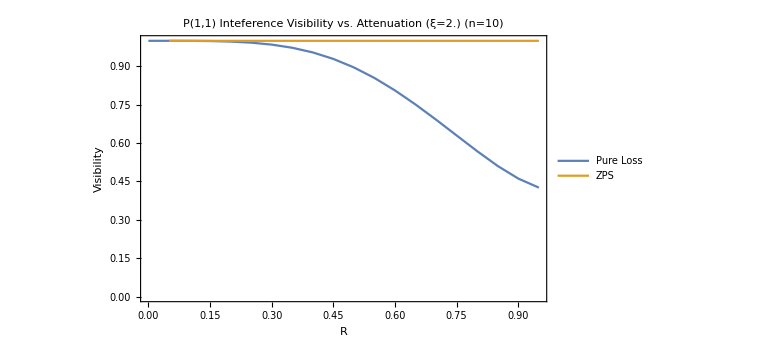

```mathematica
vsRLOSS=Table[
min=data[[2,i,-1,-1,1]];
max=data[[1,i,-1,-1,1]];
{rList[[i]],N[(max-min)/(max+min)]},{i,1,Length[rList]}];
vsRZPS=Table[
min=data[[2,i,-1,-1,2]];
max=data[[1,i,-1,-1,2]];
{rList[[i]],N[(max-min)/(max+min)]},{i,1,Length[rList]}];
ListPlot[{vsRLOSS,vsRZPS},Joined->True,Frame->True,FrameLabel->{"R","Visibility"},PlotLabel->StringJoin["P(1,1) Inteference Visibility vs. Attenuation (ξ=",ToString[xiList[[-1]]],") (n=",ToString[nList[[-1]]],")"],PlotLegends->{"Pure Loss","ZPS"}]
```

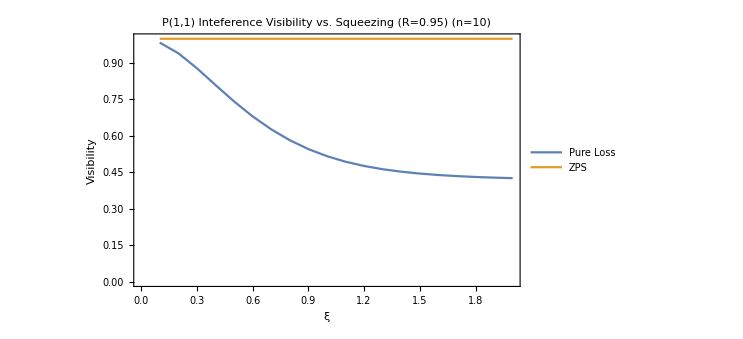

```mathematica
vsSQLOSS=Table[
min=data[[2,-1,i,-1,1]];
max=data[[1,-1,i,-1,1]];
{xiList[[i]],N[(max-min)/(max+min)]},{i,1,Length[xiList]}];
vsSQZPS=Table[
min=data[[2,-1,i,-1,2]];
max=data[[1,-1,i,-1,2]];
{xiList[[i]],N[(max-min)/(max+min)]},{i,1,Length[xiList]}];
ListPlot[{vsSQLOSS,vsSQZPS},Joined->True,Frame->True,FrameLabel->{"ξ","Visibility"},PlotLabel->StringJoin["P(1,1) Inteference Visibility vs. Squeezing (R=",ToString[rList[[-1]]],") (n=",ToString[nList[[-1]]],")"],PlotLegends->{"Pure Loss","ZPS"}]
```

## P(click,click) Interference, ideal detectors, no loss

```mathematica
Prob[ξ_,n_]:=(1/Cosh[ξ])^2(1-(Tanh[ξ])^(2(n+1)))/(1-(Tanh[ξ])^2);
S4[ξ_,n_,θ_,ϕ_]:=1/(√Prob[ξ,n])1/Cosh[ξ] Sum[(-Tanh[ξ]op4[θ,ϕ])^k/k!,{k,0,n}];
Plot[{Prob[ξ,6],Prob[ξ,10]},{ξ,0.1,2.0},PlotLegends->{"n=6","n=10"}]
```

```mathematica
ClearAll[a,b,c,d,ξ,θ,ϕ,n,PLOSS,PZPS,opCoeffs,ψ,tbl1]
a=0;  (* heralding on zero in mode a *)
b=0;  (* heralding on zero in mode b *)
(*opCoeffs[ξ_,θ_,ϕ_]:=√(c!d!)CoefficientList[CoefficientList[S2[ξ,n,θ,ϕ],{z[1],z[2]}][[c+1,d+1]],{z[3],z[4]}];*)
rList=Table[r,{r,0,0.95,0.05}];
xiList=Table[ξ,{ξ,0.0,1.0,0.1}];
nList=Table[n,{n,10,10,1}];
Monitor[
data=Table[
r = rList⟦ir⟧;
ξ = xiList⟦ix⟧;
n = nList⟦in⟧;
opCoeffs=CoefficientList[S4[ξ,n,ArcSin[r],N[ϕ]],{z[1],z[2],z[3],z[4]}];
dims=Dimensions[opCoeffs];
ψ=Table[√((k-1)!(l-1)!)opCoeffs[[k,l]],{k,1,dims[[1]]},{l,1,dims[[2]]}];
PLOSS=Table[Total[Total[Table[Abs[√((i-1)!(j-1)!)ψ[[k,l]][[i,j]]]^2,{i,1,Dimensions[ψ[[k,l]]][[1]]},{j,1,Dimensions[ψ[[k,l]]][[2]]}]]],{k,1,Dimensions[ψ][[1]]},{l,1,Dimensions[ψ][[2]]}];
PZPS=Table[Abs[√(a!b!)ψ[[k,l]][[a+1,b+1]]]^2,{k,1,Dimensions[ψ][[1]]},{l,1,Dimensions[ψ][[2]]}];
{Total[Total[PLOSS]]-Total[PLOSS,{1}][[1]]-Total[PLOSS,{2}][[1]]+PLOSS[[1,1]],
Total[Total[PZPS]]-Total[PZPS,{1}][[1]]-Total[PZPS,{2}][[1]]+PZPS[[1,1]]}
,{ϕ,0,Pi/2,Pi/2},{ir,1,Length[rList]},{ix,1,Length[xiList]},{in,1,Length[nList]}];
,{ϕ,ProgressIndicator[ir,{1,Length[rList]}],ProgressIndicator[ix,{1,Length[xiList]}],ProgressIndicator[in,{1,Length[nList]}]}]
```

Power::indet: Indeterminate expression 0.^0 encountered.

General::stop: Further output of Power::indet will be suppressed during this calculation.

$Aborted

```mathematica
Dimensions[data]
```

{2,20,11,1,2}

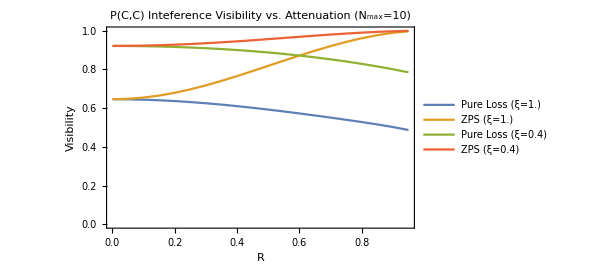

```mathematica
ListPlot[
{Transpose[{rList,Vis[data[[1,;;,-1,-1,1]],data[[2,;;,-1,-1,1]]]}],Transpose[{rList,Vis[data[[1,;;,-1,-1,2]],data[[2,;;,-1,-1,2]]]}],
Transpose[{rList,Vis[data[[1,;;,5,-1,1]],data[[2,;;,5,-1,1]]]}],
Transpose[{rList,Vis[data[[1,;;,5,-1,2]],data[[2,;;,5,-1,2]]]}]},
PlotRange->Automatic,
Joined->True,Frame->True,FrameLabel->{"R","Visibility"},PlotLabel->StringJoin["P(C,C) Inteference Visibility vs. Attenuation (N_max=",ToString[nList[[-1]]],")"],
PlotLegends->{
StringJoin["Pure Loss (ξ=",ToString[xiList[[-1]]],")"],
StringJoin["ZPS (ξ=",ToString[xiList[[-1]]],")"],
StringJoin["Pure Loss (ξ=",ToString[xiList[[5]]],")"],
StringJoin["ZPS (ξ=",ToString[xiList[[5]]],")"]
}]
```

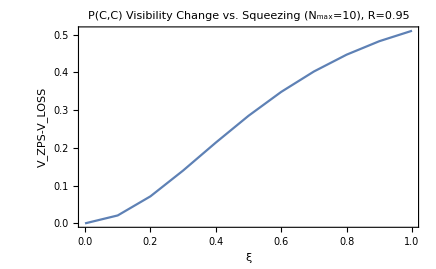

```mathematica
ListPlot[
Transpose[{xiList,Vis[data[[1,-1,;;,-1,2]],data[[2,-1,;;,-1,2]]]-Vis[data[[1,-1,;;,-1,1]],data[[2,-1,;;,-1,1]]]}],
PlotRange->Automatic,
Joined->True,Frame->True,FrameLabel->{"ξ","V_ZPS-V_LOSS"},PlotLabel->StringJoin["P(C,C) Visibility Change vs. Squeezing (N_max=",ToString[nList[[-1]]],"), R=",ToString[rList[[-1]]]]
(*,PlotLegends->{
StringJoin["Pure Loss (ξ=",ToString[xiList[[-1]]],")"],
StringJoin["ZPS (ξ=",ToString[xiList[[-1]]],")"],
StringJoin["Pure Loss (ξ=",ToString[xiList[[5]]],")"],
StringJoin["ZPS Loss (ξ=",ToString[xiList[[5]]],")"]}*)
]
```

```mathematica
ListPlot[{Transpose[{rList,Vis[data[[1,;;,-1,-1,1]],data[[2,;;,-1,-1,1]]]}],Transpose[{rList,Vis[data[[1,;;,-1,-1,2]],data[[2,;;,-1,-1,2]]]}]},Joined->True,Frame->True,FrameLabel->{"R","Visibility"},PlotLabel->StringJoin["P(C,C) Inteference Visibility vs. Attenuation (ξ=",ToString[xiList[[-1]]],") (n=",ToString[nList[[-1]]],")"],PlotLegends->{"Pure Loss","ZPS"}]
```

## P(1,1) Interference, ideal detectors, lossy input

```mathematica
(* T[ξ_,n_]=1/Cosh[ξ]∑_(k=0)^n (-Tanh[ξ]/1)^k  (ca0^k cb0^k)/(k!); (* Source: Wikipedia*)*)
(* T[ξ,n] approximates two mode squeezed vacuum up to photon number = n,n *)
S6[ξ_,n_,θl_,θt_,ϕ_]:=1/(√Prob[ξ,n])1/Cosh[ξ] Sum[(-Tanh[ξ]op6in[θl,θt,ϕ])^k/k!,{k,0,n}];
```

```mathematica
(* Approximation of taking only a few terms 1/(√Prob[n,ξ]) is to renormalize after keeping only first n=nlim terms of the sum*)
```

```mathematica
ClearAll[a,b,c,d,ξ,θ,ϕ,n,ProbLOSS,ProbZPS,opCoeffs]
a=0;  (* heralding on zero in mode a *)
b=0;  (* heralding on zero in mode b *)
c=1; (* amplitude for mode c chosen to observe the interference  *)
d=1;(* amplitude for mode d chosen to observe the interference  *)
(*opCoeffs[ξ_,θ_,ϕ_]:=√(c!d!)CoefficientList[CoefficientList[S2[ξ,n,θ,ϕ],{z[1],z[2]}][[c+1,d+1]],{z[3],z[4]}];*)
LList=Table[L,{L,0.05,0.95,0.05}];
rList=Table[r,{r,0.95,0.95,0.05}];
xiList=Table[ξ,{ξ,1.0,1.0,0.1}];
nList=Table[n,{n,4,4,1}];
data=Table[
L=LList⟦il⟧;
r = rList⟦ir⟧;
ξ = xiList⟦ix⟧;
n = nList⟦in⟧;
ψ=√(c!d!)CoefficientList[S6[ξ,n,ArcSin[L],ArcSin[r],ϕ],{z[1],z[2],z[3],z[4],z[5],z[6]}][[c+1,d+1]];
dims=Dimensions[ψ];
{ProbLOSS=Total[Table[Abs[√((i-1)!   (j-1)!(k-1)!(l-1)!)ψ[[i,j,k,l]]]^2,{i,1,Dimensions[ψ][[1]]},{j,1,Dimensions[ψ][[2]]},{k,1,Dimensions[ψ][[3]]},{l,1,Dimensions[ψ][[4]]}],4],
ProbZPS=Total[Table[Abs[√((k-1)!(l-1)!a!b!)ψ[[a+1,b+1]][[k,l]]]^2,{k,1,Dimensions[ψ[[a+1,b+1]]][[1]]},{l,1,Dimensions[ψ[[a+1,b+1]]][[2]]}],2]}
,{ϕ,0,Pi/2,Pi/2},{il,1,Length[LList]},{ir,1,Length[rList]},{ix,1,Length[xiList]},{in,1,Length[nList]}];
```

```mathematica
Dimensions[data]
Table[data[[2,1,i,-1,-1,1]],{i,1,Length[rList]}]-Table[data[[1,1,i,-1,-1,1]],{i,1,Length[rList]}]
```

{2,19,1,1,1,2}

{-0.163284}

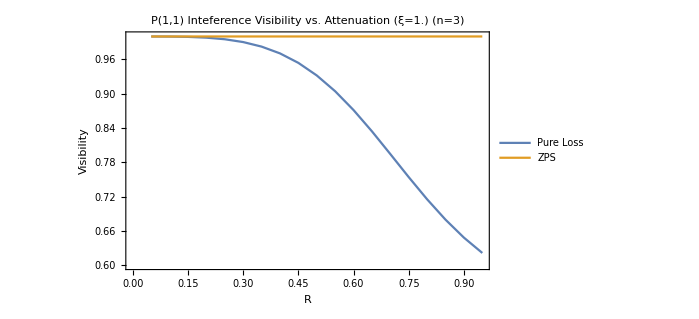

```mathematica
vsRLOSS=Table[
min=data[[2,1,i,-1,-1,1]];
max=data[[1,1,i,-1,-1,1]];
{rList[[i]],N[(max-min)/(max+min)]},{i,1,Length[rList]}];
vsRZPS=Table[
min=data[[2,1,i,-1,-1,2]];
max=data[[1,1,i,-1,-1,2]];
{rList[[i]],N[(max-min)/(max+min)]},{i,1,Length[rList]}];
ListPlot[{vsRLOSS,vsRZPS},Joined->True,Frame->True,FrameLabel->{"R","Visibility"},PlotLabel->StringJoin["P(1,1) Inteference Visibility vs. Attenuation (ξ=",ToString[xiList[[-1]]],") (n=",ToString[nList[[-1]]],")"],PlotLegends->{"Pure Loss","ZPS"}]
```

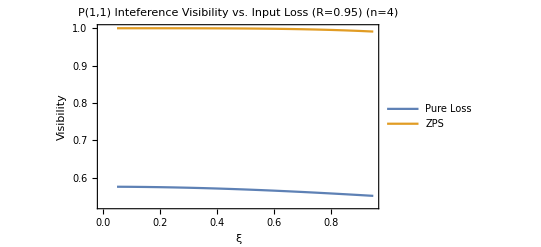

```mathematica
vsLLOSS=Table[
min=data[[2,i,-1,-1,-1,1]];
max=data[[1,i,-1,-1,-1,1]];
{LList[[i]],N[(max-min)/(max+min)]},{i,1,Length[LList]}];
vsLZPS=Table[
min=data[[2,i,-1,-1,-1,2]];
max=data[[1,i,-1,-1,-1,2]];
{LList[[i]],N[(max-min)/(max+min)]},{i,1,Length[LList]}];
ListPlot[{vsLLOSS,vsLZPS},Joined->True,Frame->True,FrameLabel->{"ξ","Visibility"},PlotLabel->StringJoin["P(1,1) Inteference Visibility vs. Input Loss (R=",ToString[rList[[-1]]],") (n=",ToString[nList[[-1]]],")"],PlotLegends->{"Pure Loss","ZPS"}]
```

## P(click,click) Interference, ideal detectors, lossy input

```mathematica
S6[ξ_,n_,θl_,θt_,ϕ_]:=1/(√Prob[ξ,n])1/Cosh[ξ] Sum[(-Tanh[ξ]op6in[θl,θt,ϕ])^k/k!,{k,0,n}];
PClick[P_]:=Total[P,2]-Total[P,{1}][[1]]-Total[P,{2}][[1]]+P[[1,1]];
ClearAll[a,b,c,d,ξ,θ,ϕ,n,PLOSS,PZPS,opCoeffs,ψ,tbl1]
a=0;  (* heralding on zero in mode a *)
b=0;  (* heralding on zero in mode b *)
(*opCoeffs[ξ_,θ_,ϕ_]:=√(c!d!)CoefficientList[CoefficientList[S2[ξ,n,θ,ϕ],{z[1],z[2]}][[c+1,d+1]],{z[3],z[4]}];*)
LList=Table[L,{L,0.1,0.9,0.1}];
rList={0.1,0.5,0.9};(*Table[r,{r,0.5,0.5,0.1}];*)
xiList=Table[ξ,{ξ,0.5,0.5,0.1}];
nList=Table[n,{n,5,5,1}];
Monitor[
data=Table[
L=LList[[il]];
r = rList⟦ir⟧;
ξ = xiList⟦ix⟧;
n = nList⟦in⟧;
opCoeffs=CoefficientList[S6[ξ,n,ArcSin[L],ArcSin[r],ϕ],{z[1],z[2],z[3],z[4],z[5],z[6]}];
dims=Dimensions[opCoeffs];
ψ=Table[√((g-1)!(h-1)!(i-1)!(j-1)!(k-1)!(l-1)!)opCoeffs[[g,h,i,j,k,l]],{g,1,dims[[1]]},{h,1,dims[[2]]},{i,1,dims[[3]]},{j,1,dims[[4]]},{k,1,dims[[5]]},{l,1,dims[[6]]}];
PLOSS=Table[Total[Table[Abs[ψ[[g,h]][[i,j,k,l]]]^2,{i,1,Dimensions[ψ[[g,h]]][[1]]},{j,1,Dimensions[ψ[[g,h]]][[2]]},{k,1,Dimensions[ψ[[g,h]]][[3]]},{l,1,Dimensions[ψ[[g,h]]][[4]]}],4],{g,1,Dimensions[ψ][[1]]},{h,1,Dimensions[ψ][[1]]}];
PZPS=Table[Total[Table[Abs[ψ[[g,h]][[a+1,b+1,k,l]]]^2,{k,1,Dimensions[ψ[[g,h]][[a+1,b+1]]][[1]]},{l,1,Dimensions[ψ[[g,h]][[a+1,b+1]]][[2]]}],2],{g,1,Dimensions[ψ][[1]]},{h,1,Dimensions[ψ][[2]]}];
{PClick[PLOSS],PClick[PZPS]}
,{ϕ,0,Pi/2,Pi/2},{il,1,Length[LList]},{ir,1,Length[rList]},{ix,1,Length[xiList]},{in,1,Length[nList]}];
,{ϕ,ProgressIndicator[il,{1,Length[LList]}],ProgressIndicator[ir,{1,Length[rList]}],ProgressIndicator[ix,{1,Length[xiList]}],ProgressIndicator[in,{1,Length[nList]}]}]
```

$Aborted

```mathematica
Dimensions[data]
```

{2,9,3,1,1,2}

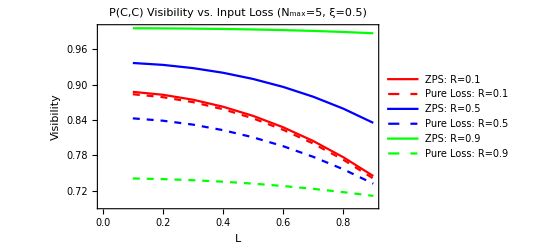

```mathematica
ListPlot[
{Transpose[{LList,Vis[data[[1,;;,1,-1,-1,2]],data[[2,;;,1,-1,-1,2]]]}],
Transpose[{LList,Vis[data[[1,;;,1,-1,-1,1]],data[[2,;;,1,-1,-1,1]]]}],
Transpose[{LList,Vis[data[[1,;;,2,-1,-1,2]],data[[2,;;,2,-1,-1,2]]]}],
Transpose[{LList,Vis[data[[1,;;,2,-1,-1,1]],data[[2,;;,2,-1,-1,1]]]}],
Transpose[{LList,Vis[data[[1,;;,3,-1,-1,2]],data[[2,;;,3,-1,-1,2]]]}],
Transpose[{LList,Vis[data[[1,;;,3,-1,-1,1]],data[[2,;;,3,-1,-1,1]]]}]},
PlotRange->Automatic,
Joined->True,Frame->True,FrameLabel->{"L","Visibility"},PlotLabel->StringJoin["P(C,C) Visibility vs. Input Loss (N_max=",ToString[nList[[-1]]],", ξ=",ToString[xiList[[-1]]],")"],PlotStyle->{{Red},{Red,Dashed},{Blue},{Blue,Dashed},{Green},{Green,Dashed}}
,PlotLegends->{StringJoin["ZPS: R=",ToString[rList[[1]]]],StringJoin["Pure Loss: R=",ToString[rList[[1]]]],StringJoin["ZPS: R=",ToString[rList[[2]]]],StringJoin["Pure Loss: R=",ToString[rList[[2]]]],StringJoin["ZPS: R=",ToString[rList[[3]]]],StringJoin["Pure Loss: R=",ToString[rList[[3]]]]}
]
```

## P(click,click) Interference, ideal detectors, lossy heralding

```mathematica
ClearAll[S6,a,b,c,d,ξ,θ,ϕ,n,PLOSS,PZPS,opCoeffs,ψ,data]
S6[ξ_,n_,θl_,θt_,ϕ_]:=1/(√Prob[ξ,n])1/Cosh[ξ] Sum[(-Tanh[ξ]op6hoz[θl,θt,ϕ])^k/k!,{k,0,n}];
PClick[P_]:=Total[P,2]-Total[P,{1}][[1]]-Total[P,{2}][[1]]+P[[1,1]];

a=0;  (* heralding on zero in mode a *)
b=0;  (* heralding on zero in mode b *)
(*opCoeffs[ξ_,θ_,ϕ_]:=√(c!d!)CoefficientList[CoefficientList[S2[ξ,n,θ,ϕ],{z[1],z[2]}][[c+1,d+1]],{z[3],z[4]}];*)
LList=Table[L,{L,0.1,0.9,0.1}];
rList={0,0.95};(*Table[r,{r,0,0.95,0.05}];*)
xiList=Table[ξ,{ξ,0.5,0.5,0.1}];
nList=Table[n,{n,5,5,1}];
Monitor[
data=Table[
L=LList[[il]];
r = rList⟦ir⟧;
ξ = xiList⟦ix⟧;
n = nList⟦in⟧;
opCoeffs=CoefficientList[S6[ξ,n,ArcSin[L],ArcSin[r],ϕ],{z[1],z[2],z[3],z[4],z[5],z[6]}];
dims=Dimensions[opCoeffs];
ψ=Table[√((g-1)!(h-1)!(i-1)!(j-1)!(k-1)!(l-1)!)opCoeffs[[g,h,i,j,k,l]],{g,1,dims[[1]]},{h,1,dims[[2]]},{i,1,dims[[3]]},{j,1,dims[[4]]},{k,1,dims[[5]]},{l,1,dims[[6]]}];
PLOSS=Table[Total[Table[Abs[ψ[[g,h]][[i,j,k,l]]]^2,{i,1,Dimensions[ψ[[g,h]]][[1]]},{j,1,Dimensions[ψ[[g,h]]][[2]]},{k,1,Dimensions[ψ[[g,h]]][[3]]},{l,1,Dimensions[ψ[[g,h]]][[4]]}],4],{g,1,Dimensions[ψ][[1]]},{h,1,Dimensions[ψ][[1]]}];
PZPS=Table[Total[Table[Abs[ψ[[g,h]][[a+1,b+1,k,l]]]^2,{k,1,Dimensions[ψ[[g,h]][[a+1,b+1]]][[1]]},{l,1,Dimensions[ψ[[g,h]][[a+1,b+1]]][[2]]}],2],{g,1,Dimensions[ψ][[1]]},{h,1,Dimensions[ψ][[2]]}];
{PClick[PLOSS],PClick[PZPS]}
,{ϕ,0,Pi/2,Pi/2},{il,1,Length[LList]},{ir,1,Length[rList]},{ix,1,Length[xiList]},{in,1,Length[nList]}];
,{ϕ,ProgressIndicator[il,{1,Length[LList]}],ProgressIndicator[ir,{1,Length[rList]}],ProgressIndicator[ix,{1,Length[xiList]}],ProgressIndicator[in,{1,Length[nList]}]}]
```

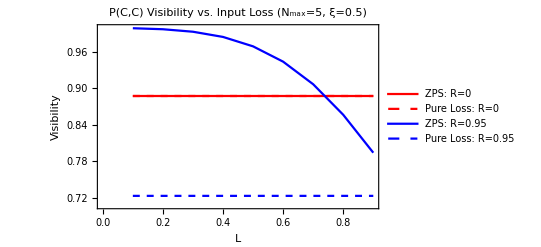

```mathematica
ListPlot[
{Transpose[{LList,Vis[data[[1,;;,1,-1,-1,2]],data[[2,;;,1,-1,-1,2]]]}],
Transpose[{LList,Vis[data[[1,;;,1,-1,-1,1]],data[[2,;;,1,-1,-1,1]]]}],
Transpose[{LList,Vis[data[[1,;;,2,-1,-1,2]],data[[2,;;,2,-1,-1,2]]]}],
Transpose[{LList,Vis[data[[1,;;,2,-1,-1,1]],data[[2,;;,2,-1,-1,1]]]}]},
PlotRange->Automatic,
Joined->True,Frame->True,FrameLabel->{"L","Visibility"},PlotLabel->StringJoin["P(C,C) Visibility vs. Input Loss (N_max=",ToString[nList[[-1]]],", ξ=",ToString[xiList[[-1]]],")"],PlotStyle->{{Red},{Red,Dashed},{Blue},{Blue,Dashed},{Green},{Green,Dashed}}
,PlotLegends->{StringJoin["ZPS: R=",ToString[rList[[1]]]],StringJoin["Pure Loss: R=",ToString[rList[[1]]]],StringJoin["ZPS: R=",ToString[rList[[2]]]],StringJoin["Pure Loss: R=",ToString[rList[[2]]]]}
]
```

## P(click,click) Interference, ideal detectors, lossy input

```mathematica
S6[ξ_,n_,θl_,θt_,ϕ_]:=1/(√Prob[ξ,n])1/Cosh[ξ] Sum[(-Tanh[ξ]op6out[θl,θt,ϕ])^k/k!,{k,0,n}];
PClick[P_]:=Total[P,2]-Total[P,{1}][[1]]-Total[P,{2}][[1]]+P[[1,1]];
ClearAll[a,b,c,d,ξ,θ,ϕ,n,PLOSS,PZPS,opCoeffs,ψ,tbl1]
a=0;  (* heralding on zero in mode a *)
b=0;  (* heralding on zero in mode b *)
(*opCoeffs[ξ_,θ_,ϕ_]:=√(c!d!)CoefficientList[CoefficientList[S2[ξ,n,θ,ϕ],{z[1],z[2]}][[c+1,d+1]],{z[3],z[4]}];*)
LList=Table[L,{L,0.1,0.9,0.1}];
rList={0.1,0.5,0.9};(*Table[r,{r,0.5,0.5,0.1}];*)
xiList=Table[ξ,{ξ,0.5,0.5,0.1}];
nList=Table[n,{n,5,5,1}];
Monitor[
data=Table[
L=LList[[il]];
r = rList⟦ir⟧;
ξ = xiList⟦ix⟧;
n = nList⟦in⟧;
opCoeffs=CoefficientList[S6[ξ,n,ArcSin[L],ArcSin[r],ϕ],{z[1],z[2],z[3],z[4],z[5],z[6]}];
dims=Dimensions[opCoeffs];
ψ=Table[√((g-1)!(h-1)!(i-1)!(j-1)!(k-1)!(l-1)!)opCoeffs[[g,h,i,j,k,l]],{g,1,dims[[1]]},{h,1,dims[[2]]},{i,1,dims[[3]]},{j,1,dims[[4]]},{k,1,dims[[5]]},{l,1,dims[[6]]}];
PLOSS=Table[Total[Table[Abs[ψ[[g,h]][[i,j,k,l]]]^2,{i,1,Dimensions[ψ[[g,h]]][[1]]},{j,1,Dimensions[ψ[[g,h]]][[2]]},{k,1,Dimensions[ψ[[g,h]]][[3]]},{l,1,Dimensions[ψ[[g,h]]][[4]]}],4],{g,1,Dimensions[ψ][[1]]},{h,1,Dimensions[ψ][[1]]}];
PZPS=Table[Total[Table[Abs[ψ[[g,h]][[a+1,b+1,k,l]]]^2,{k,1,Dimensions[ψ[[g,h]][[a+1,b+1]]][[1]]},{l,1,Dimensions[ψ[[g,h]][[a+1,b+1]]][[2]]}],2],{g,1,Dimensions[ψ][[1]]},{h,1,Dimensions[ψ][[2]]}];
{PClick[PLOSS],PClick[PZPS]}
,{ϕ,0,Pi/2,Pi/2},{il,1,Length[LList]},{ir,1,Length[rList]},{ix,1,Length[xiList]},{in,1,Length[nList]}];
,{ϕ,ProgressIndicator[il,{1,Length[LList]}],ProgressIndicator[ir,{1,Length[rList]}],ProgressIndicator[ix,{1,Length[xiList]}],ProgressIndicator[in,{1,Length[nList]}]}]
```

```mathematica
Dimensions[data]
```

{2,9,3,1,1,2}

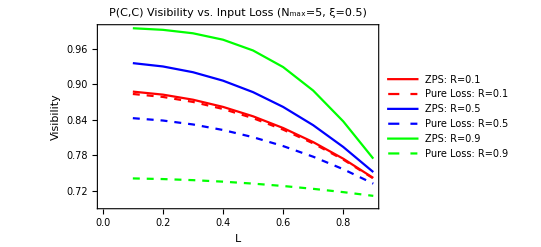

```mathematica
ListPlot[
{Transpose[{LList,Vis[data[[1,;;,1,-1,-1,2]],data[[2,;;,1,-1,-1,2]]]}],
Transpose[{LList,Vis[data[[1,;;,1,-1,-1,1]],data[[2,;;,1,-1,-1,1]]]}],
Transpose[{LList,Vis[data[[1,;;,2,-1,-1,2]],data[[2,;;,2,-1,-1,2]]]}],
Transpose[{LList,Vis[data[[1,;;,2,-1,-1,1]],data[[2,;;,2,-1,-1,1]]]}],
Transpose[{LList,Vis[data[[1,;;,3,-1,-1,2]],data[[2,;;,3,-1,-1,2]]]}],
Transpose[{LList,Vis[data[[1,;;,3,-1,-1,1]],data[[2,;;,3,-1,-1,1]]]}]},
PlotRange->Automatic,
Joined->True,Frame->True,FrameLabel->{"L","Visibility"},PlotLabel->StringJoin["P(C,C) Visibility vs. Input Loss (N_max=",ToString[nList[[-1]]],", ξ=",ToString[xiList[[-1]]],")"],PlotStyle->{{Red},{Red,Dashed},{Blue},{Blue,Dashed},{Green},{Green,Dashed}}
,PlotLegends->{StringJoin["ZPS: R=",ToString[rList[[1]]]],StringJoin["Pure Loss: R=",ToString[rList[[1]]]],StringJoin["ZPS: R=",ToString[rList[[2]]]],StringJoin["Pure Loss: R=",ToString[rList[[2]]]],StringJoin["ZPS: R=",ToString[rList[[3]]]],StringJoin["Pure Loss: R=",ToString[rList[[3]]]]}
]
```

# Quantum states

## Squeezed states through Noiseless Attenuation

## Original

```mathematica
ClearAll[matsq,ξ,k,x]
ψsq[ξ_,nlim_,x_]=1/(√Cosh[ξ])∑_(k=0)^nlim √Binomial[2k,k](-Tanh[ξ]/2)^k(ⅇ^(-x^2/2)/(π^(1/4)√((2k)!2^(2k))))HermiteH[2k,x];(*ca0^(2k)/(√((2k)!));*)
nlim=10;
Wsq[ξ_,nlim_,x_,p_]:=(1/(2π))NIntegrate[ⅇ^(-ⅈ p y)Conjugate[(ψsq[ξ,nlim,x-y/2])] ψsq[ξ,nlim,x+y/2],{y,-10,10}];
limits=3;
range=10;
s=3;
ξ=1/2 Log[s];
Monitor[
matsq=Table[Re[Chop[Wsq[ξ,nlim,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{x,1,2 range +1}]
,{p,x}];
```

```mathematica
Dimensions[matsq]
```

{21,21}

#### s = 3

```mathematica
ListPlot3D[matsq,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->Function[{x,p,W},ColorData["Rainbow"][W+0.275]],ColorFunctionScaling->True,PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

Model Fitting

```mathematica
ClearAll[a,s,p,x]
model=a Exp[(-(s x^2+p^2/s))/(2 σ^2)];
range =(Dimensions[matsq][[1]]-1)/2;
IdxData= Table[{(i-range -1)limits/range,(j-range-1)limits/range,matsq[[i,j]]},{i,1,2range+1},{j,1,2range+1}];
Data=Flatten[IdxData,1];
fit = FindFit[Data,model,{{a,1/π},{σ,1/(√2)},{s,1}},{p,x}]
```

{a→0.31831,σ→0.707107,s→3.}

## After beam splitter

```mathematica
ClearAll[s,ξ,r,t,ca,cb,nlim]
B[r_,t_]={{t,ⅈ r},{ⅈ r,t}}; 
{ca0,cb0}=B[𝓇,𝓉].{ca,cb};
ψn[n_,x_]=(ⅇ^(-x^2/2)/(π^(1/4)√(n!2^n)))HermiteH[n,x];
ψin[ξ_,nlim_]=Expand[1/(√Cosh[ξ])∑_(k=0)^nlim √Binomial[2k,k](-Tanh[ξ]/2)^k ca0^(2k)/(√((2k)!))];
b=0;(* Post selection *)
s=3;
ξ=1/2 Log[s];
nlim=10;
coefftable=CoefficientList[ψin[ξ,nlim],{cb,ca}];
Pr=Chop[Table[Abs[√((i-1)!   (j-1)!)coefftable[[i,j]]]^2,{i,1,Dimensions[coefftable][[1]]},{j,1,Dimensions[coefftable][[2]]}]];
Dimensions[coefftable]
```

{21,21}

```mathematica
𝓇=√0.5;
𝓉=√(1-𝓇^2);
Total[Pr,{2}][[0+1]]
```

0.894427

```mathematica
Psucc =∑_(k=0)^20 Abs[(√Binomial[2k,k])/(√Cosh[1/2 Log[3]])(-Tanh[1/2 Log[3]]/2)^k]^2(√0.5)^(2(2k))
```

0.894427

### w/ post selection

```mathematica
ψoutwps[x_]=FullSimplify[Total[Table[√(b!(i-1)!)coefftable[[b+1,i]]ψn[i-1,x],{i,1,Dimensions[coefftable][[2]]}]]];
```

#### results

```mathematica
𝓇=√0.5;
𝓉=√(1-𝓇^2);
Wwps[x_,p_]:=(1/(Total[Pr,{2}][[b+1]]2π))NIntegrate[ⅇ^(-ⅈ p y)Conjugate[(ψoutwps[x-(1/2)y])] ψoutwps[x+(1/2)y],{y,-10,10}];
limits=3;
range=10;
Monitor[
wpsmat=Table[Re[Chop[Wwps[(x-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{x,1,2 range +1}]
,{p,x}];
Total[wpsmat,2](limits/range)^2
```

0.999472

𝓇=√0.5

```mathematica
ListPlot3D[wpsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->Function[{x,p,W},ColorData["Rainbow"][W+0.275]],ColorFunctionScaling->True,PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

#### Fit

𝓇=√0.5

```mathematica
ClearAll[a,σ,s,p,x]
model=a Exp[(-(s x^2+p^2/s))/(2 σ^2)];
range =(Dimensions[wpsmat][[1]]-1)/2;
IdxData= Table[{(i-range -1)limits/range,(j-range-1)limits/range,wpsmat[[i,j]]},{i,1,2range+1},{j,1,2range+1}];
Data=Flatten[IdxData,1];
fit = FindFit[Data,model,{{a,1/π},{σ,1/(√2)},{s,1}},{p,x}]
```

{a→0.31831,σ→0.707107,s→1.66667}

### w/o post selection

```mathematica
ψoutwops[x_]=Total[Table[√((i-1)!(j-1)!)coefftable[[i,j]]ψn[j-1,x],{i,1,Dimensions[coefftable][[1]]},{j,1,Dimensions[coefftable][[2]]}],{2}];

𝓇=√0.5;
𝓉=√(1-𝓇^2);
(*Wwops[x_,p_]:=Total[Table[(Total[Pr,{2}][[i]]/(2π))NIntegrate[ⅇ^(-ⅈ p y)(ψoutwops[x-(1/2)y][[i]])^*ψoutwops[x+(1/2)y][[i]],{y,-10,10}],{i,Dimensions[coefftable][[1]]}]];*)
Wwops[x_,p_]:=Total[Table[1/(2π)NIntegrate[ⅇ^(-ⅈ p y)Conjugate[(ψoutwops[x-(1/2)y][[i]])] ψoutwops[x+(1/2)y][[i]],{y,-10,10}],{i,Dimensions[coefftable][[1]]}]];
limits=3;
range=10;
Monitor[
wopsmat=Table[Re[Chop[Wwops[(x-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{x,1,2 range +1}]
,{p,x}];
Total[wopsmat,2](limits/range)^2
```

0.998432

𝓇=√0.5

```mathematica
ListPlot3D[wopsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->Function[{x,p,W},ColorData["Rainbow"][W+0.275]],ColorFunctionScaling->True,PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

#### Fit

𝓇=√0.5

```mathematica
ClearAll[a,σ,s,p,x]
model=a Exp[(-(s x^2+p^2/s))/(2 σ^2)];
range =(Dimensions[wopsmat][[1]]-1)/2;
IdxData= Table[{(i-range -1)limits/range,(j-range-1)limits/range,wopsmat[[i,j]]},{i,1,2range+1},{j,1,2range+1}];
Data=Flatten[IdxData,1];
fit = FindFit[Data,model,{{a,1/π},{σ,1/(√2)},{s,1}},{p,x}]
```

{a→0.275664,σ→0.759836,s→1.73205}

```mathematica
{√(1/(π a/.fit)),(√2 σ/.fit)^1}
```

{1.07457,1.07457}

## Cat States through noiseless attenuation

### Calculation of the Wigner function using number states (and approx. by taking few terms) before Noiseless Attenuation

```mathematica
Psucc[α_,nlim_,t_]=∑_(n=0)^nlim Abs[((( α)^n+( -α)^n)/(√(4 Cosh[Abs[α]^2])√(n!)))]^2 t^(2n);(* Success Probability using formula *)
```

$Aborted

```mathematica
Simplify[∑_(n=0)^20 Abs[((( 2)^n+( -2)^n)/(√(4 Cosh[Abs[2]^2])√(n!)))]^2(√0.5)^(2n),𝓉∈Reals]
```

0.137768

```mathematica
(( 2)^1+( -2)^1)/(√(4 Cosh[Abs[2]^2])√(1!))
```

0

```mathematica
ψn[n_,x_]=(ⅇ^(-x^2/2)/(π^(1/4)√(n!2^n)))HermiteH[n,x];
ψc[α_,nlim_,x_]=ⅇ^((-Abs[α]^2)/2)∑_(n=0)^nlim (α^n (ⅇ^(-x^2/2)/(π^(1/4)√(n!2^n)))HermiteH[n,x] )/(√n!);
ψcExact[α_,nlim_,x_]=(1/π^(1/4))ⅇ^((-(x-√2 α)^2)/2);(*checked*)
ψCat[α_,nlim_,x_]=(ψc[α,nlim,x]+ψc[-α,nlim,x])/(√(2(1+ⅇ^(-2 Abs[α]^2))));

nlim=20;
WCat[α_,nlim_,x_,p_]:=(1/(2π))NIntegrate[ⅇ^(-ⅈ p y)Conjugate[(ψCat[α,nlim,x-y/2])] ψCat[α,nlim,x+y/2],{y,-10,10}];
WCatExact[α_,nlim_,x_,p_]:=(ⅇ^(-(x-√2 α)^2-p^2)+ⅇ^(-(x+√2 α)^2-p^2)+2 ⅇ^(-x^2-p^2)Cos[2 √2 α p])/(2π(1+ⅇ^(-2 Abs[α]^2)));(* Typo in https://arxiv.org/pdf/2006.16985.pdf Eq. (27) *)
```

```mathematica
limits=5;
range=10;
α=2;
matCatExact2=Table[Re[Chop[WCatExact[α,nlim,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{x,1,2 range +1}];
```

```mathematica
Monitor[
matCat=Table[Re[Chop[WCat[α,nlim,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{x,1,2 range +1}]
,{p,x}]
```

$Aborted

```mathematica
NIntegrate[WCat[2,0,x,p],{x,-5,5},{p,-5,5}]
```

0.998934

```mathematica
ListPlot3D[matCatExact2,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->Function[{x,p,W},ColorData["Rainbow"][W-0.155]],ColorFunctionScaling->True,PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

```mathematica
N[Total[Total[matCatExact2]]](limits/range)^2
```

0.99977

### Calculation of the Wigner function using number states (and approx. by taking few terms) after Noiseless Attenuation

```mathematica
{{|Subscript[ψ, cat]⟩=1/(√(cosh(|α|)^2))∑_(Subscript[n, a]=0)^∞ ∑_(Subscript[n, b]=0)^∞ f(Subscript[n, a],Subscript[n, b])}, {×((tα)^Subscript[n, a](irα)^Subscript[n, b])/(√(Subscript[n, a]!Subscript[n, b]!))|Subscript[n, a]⟩|Subscript[n, b]⟩,}}
```

```mathematica
ψin[α_,nlim_]=Expand[1/(√Cosh[Abs[α]^2])∑_(na=0)^nlim ∑_(nb=0)^nlim (Mod[na+nb+1,2]((𝓉 α)^na(ⅈ 𝓇 α)^nb ca^na cb^nb)/((na!) (nb!)))];
α=2;
nlim=20;

coefftable=CoefficientList[ψin[α,nlim],{cb,ca}];

ψn[n_,x_]=(ⅇ^(-x^2/2)/(π^(1/4)√(n!2^n)))HermiteH[n,x];

OptoN = Table[√((i-1)!(j-1)!),{i,1,Dimensions[coefftable][[1]]},{j,1,Dimensions[coefftable][[2]]}];
Pr=Chop[(OptoN coefftable)*  (OptoN coefftable)];
(*Pr=Chop[Table[Abs[√((i-1)!   (j-1)!)coefftable[[i,j]]]^2,{i,1,Dimensions[coefftable][[1]]},{j,1,Dimensions[coefftable][[2]]}]];*)
Dimensions[coefftable]
NumberStates[x_]=Table[ψn[i-1,x],{i,1,Dimensions[coefftable][[2]]}];
b=0;
```

{21,21}

```mathematica
ψin[α,nlim]
```

```mathematica
Simplify[Cosh[4]Total[Pr[[1]]],𝓉∈Reals]//MatrixForm
```

1+8 𝓉^4+(32 𝓉^8)/3+(256 𝓉^12)/45+(512 𝓉^16)/315+(4096 𝓉^20)/14175+(16384 𝓉^24)/467775+(131072 𝓉^28)/42567525+(131072 𝓉^32)/638512875+(1048576 𝓉^36)/97692469875+(4194304 𝓉^40)/9280784638125

```mathematica
Simplify[Cosh[4]Total[Pr,{2}][[0+1]],𝓉∈Reals]
```

1+8 𝓉^4+(32 𝓉^8)/3+(256 𝓉^12)/45+(512 𝓉^16)/315+(4096 𝓉^20)/14175+(16384 𝓉^24)/467775+(131072 𝓉^28)/42567525+(131072 𝓉^32)/638512875+(1048576 𝓉^36)/97692469875+(4194304 𝓉^40)/9280784638125

```mathematica
(*B[r_,t_]={{t,ⅈ r},{ⅈ r,t}}; 
{ca0,cb0}=B[𝓇,𝓉].{ca,cb};
ψn[n_,x_]=(ⅇ^(-x^2/2)/(π^(1/4)√(n!2^n)))HermiteH[n,x];
ψin[α_,nlim_]=Expand[1/(√(2((1+ⅇ^(-2 Abs[α]^2)))))(ⅇ^((-Abs[α]^2)/2)∑_(n=0)^nlim ((α^n +(-α)^n)ca0^n )/n!)];
b=0;(* Post selection *)
α=2;
nlim=20;
coefftable=CoefficientList[ψin[α,nlim],{cb,ca}];
OptoN = Table[√((i-1)!(j-1)!),{i,1,Dimensions[coefftable][[1]]},{j,1,Dimensions[coefftable][[2]]}];
Pr=Chop[(OptoN coefftable)*  (OptoN coefftable)];
(*Pr=Chop[Table[Abs[√((i-1)!   (j-1)!)coefftable[[i,j]]]^2,{i,1,Dimensions[coefftable][[1]]},{j,1,Dimensions[coefftable][[2]]}]];*)
Dimensions[coefftable]
NumberStates[x_]=Table[ψn[i-1,x],{i,1,Dimensions[coefftable][[2]]}];*)
```

{21,21}

```mathematica
𝓉=√0.5;
Total[Pr,{2}][[0+1]]
```

0.137768

### w/ post selection

```mathematica
ψoutwps[x_]=FullSimplify[Total[OptoN[[b+1,All]] coefftable[[b+1,All]] NumberStates[x]]];
```

```mathematica
(*ψoutwps[x_]=FullSimplify[Total[Table[√(b!(i-1)!)coefftable[[b+1,i]]ψn[i-1,x],{i,1,Dimensions[coefftable][[2]]}]]];*)
```

#### results

```mathematica
𝓇=√0.5;
𝓉=√(1-𝓇^2);
Wwps[x_,p_]:=(1/(Total[Pr,{2}][[b+1]]2π))NIntegrate[ⅇ^(-ⅈ p y)Conjugate[(ψoutwps[x-(1/2)y])] ψoutwps[x+(1/2)y],{y,-10,10}];
limits=5;
range=10;
Monitor[
wpsmat=Table[Re[Chop[Wwps[(x-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{x,1,2 range +1}]
,{p,x}];
Total[wpsmat,2](limits/range)^2
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0193758}. NIntegrate obtained 7.058×10^-16-7.27919×10^-23 ⅈ and 5.16033×10^-21 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0193758}. NIntegrate obtained -1.19404×10^-15-5.08271×10^-21 ⅈ and 4.81036×10^-20 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.624845}. NIntegrate obtained -1.6465×10^-13-1.01644×10^-20 ⅈ and 3.41075×10^-19 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

0.999999

```mathematica
Total[Pr,{2}][[1]]
```

0.137768

```mathematica
ListPlot3D[wpsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->Function[{x,p,W},ColorData["Rainbow"][W-0.040]],ColorFunctionScaling->True,PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

r = √0.5

```mathematica
ListPlot3D[wpsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->Function[{x,p,W},ColorData["Rainbow"][W-0.040]],ColorFunctionScaling->True,PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

r = 0.5

```mathematica
ListPlot3D[wpsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

r = 0

```mathematica
ListPlot3D[wpsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

### w/o post selection

```mathematica
ψoutwops[x_]=Total[Table[(coefftable OptoN)[[i,j]] NumberStates[x][[j]],{i,1,Dimensions[coefftable][[1]]},{j,1,Dimensions[coefftable][[2]]}] ,{2}];
(*Total[ coefftable OptoN  ConstantArray[NumberStates[x],Dimensions[coefftable][[1]]],{2}];*)
(*ψoutwops[x_]=Total[Table[√((i-1)!(j-1)!)coefftable[[i,j]]ψn[j-1,x],{i,1,Dimensions[coefftable][[1]]},{j,1,Dimensions[coefftable][[2]]}],{2}];*)
Dimensions[ψoutwops[x]]
```

{21}

#### results

```mathematica
𝓇=√0.5;
𝓉=√(1-𝓇^2);
(*Wwops[x_,p_]:=Total[Table[(Total[Pr,{2}][[i]]/(2π))NIntegrate[ⅇ^(-ⅈ p y)(ψoutwops[x-(1/2)y][[i]])^*ψoutwops[x+(1/2)y][[i]],{y,-10,10}],{i,Dimensions[coefftable][[1]]}]];*)
Wwops[x_,p_]:=Total[Table[1/(2π)NIntegrate[ⅇ^(-ⅈ p y)Conjugate[(ψoutwops[x-(1/2)y][[i]])] ψoutwops[x+(1/2)y][[i]],{y,-10,10}],{i,Dimensions[coefftable][[1]]}]];
```

```mathematica
limits=5;
range=10;
Monitor[
wopsmat=Table[Re[Chop[Wwops[(x-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{x,1,2 range +1}],
{p,x}];
Total[wopsmat,2](limits/range)^2
```

0.999999

r = √0.5

```mathematica
ListPlot3D[wopsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->Function[{x,p,W},ColorData["Rainbow"][W+0.275]],ColorFunctionScaling->True,PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

r = 0.5

```mathematica
ListPlot3D[wopsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

r = 0

```mathematica
ListPlot3D[wopsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

## Model fitting

```mathematica
ListPlot3D[wpsmat,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

### Before

```mathematica
ClearAll[A,α]
model=1((ⅇ^(-(x-√2 α)^2-p^2)+ⅇ^(-(x+√2 α)^2-p^2)+2 ⅇ^(-x^2-p^2)Cos[2 √2 α p])/(2π(1+ⅇ^(-2 Abs[α]^2))));
range =(Dimensions[matCatExact2][[1]]-1)/2;
IdxData= Table[{(i-range -1)limits/range,(j-range-1)limits/range,matCatExact2[[i,j]]},{i,1,2range+1},{j,1,2range+1}];
Data=Flatten[IdxData,1];
fit = FindFit[Data,model,{{A,1},{α,2}},{p,x}]
```

FindFit::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{A→1.,α→2.}

```mathematica
limits=5;
range=10;
α=α/.fit;
matCatExact=Table[Re[Chop[WCatExact[α,nlim,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{x,1,2 range +1}];
ListPlot3D[matCatExact,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

### After (w/ post selection)

```mathematica
ClearAll[A,α]
model=1((ⅇ^(-(x-√2 α)^2-p^2)+ⅇ^(-(x+√2 α)^2-p^2)+2 ⅇ^(-x^2-p^2)Cos[2 √2 α p])/(2π(1+ⅇ^(-2 Abs[α]^2))));
range =(Dimensions[wpsmat][[1]]-1)/2;
IdxData= Table[{(i-range -1)limits/range,(j-range-1)limits/range,wpsmat[[i,j]]},{i,1,2range+1},{j,1,2range+1}];
Data=Flatten[IdxData,1];
fit = FindFit[Data,model,{{A,1},{α,2}},{p,x}]
WCatExact[α_,nlim_,x_,p_]:=(ⅇ^(-(x-√2 α)^2-p^2)+ⅇ^(-(x+√2 α)^2-p^2)+2 ⅇ^(-x^2-p^2)Cos[2 √2 α p])/(2π(1+ⅇ^(-2 Abs[α]^2)));(* Typo in https://arxiv.org/pdf/2006.16985.pdf Eq. (27) *)
limits=5;
range=10;
matCatExact2=Table[Re[Chop[WCatExact[α/.fit,nlim,(x-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{x,1,2 range +1}];
ListPlot3D[matCatExact2,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

{A→1.,α→1.41422}

-Graphics3D-

This tells the cat state is noiseless after post selection

## Effect of inefficient detector in noiseless attenuation

```mathematica
B[r_,t_]={{t,ⅈ r},{ⅈ r,t}}; 
{ca0,cb0}=B[𝓇,𝓉].{ca,cb1};
{cb1,cdump0}=B[𝓇loss,𝓉loss].{cb,cdump};
ψn[n_,x_]=(ⅇ^(-x^2/2)/(π^(1/4)√(n!2^n)))HermiteH[n,x];
(*ψin[α_,n_]=Expand[1/(√Cosh[Abs[α]^2])(∑_(n=0)^nlim ((α^n +(-α)^n)Simplify[ca0^n])/(n!))];*)
ψin[α_,n_]=Expand[ ca0^0/(√3 √(0!))+ca0^1/(√3 √(1!))+ca0^2/(√3 √(2!))];
b=0;(* Post selection *)
α=2;
(* nlim=20;*)
nlim =2;
coefftable=CoefficientList[ψin[α,nlim],{cb,cdump,ca}];
Pr=ComplexExpand[Chop[Table[Abs[coefftable[[i,j,k]] √((i-1)!   (j-1)!(k-1)!)]^2,{i,1,Dimensions[coefftable][[1]]},{j,1,Dimensions[coefftable][[2]]},{k,1,Dimensions[coefftable][[3]]}]]];
Dimensions[coefftable]
```

{3,3,3}

```mathematica
coefftable//MatrixForm
```

((1/(√3)
𝓉/(√3)
𝓉^2/(√6)) | (-(𝓇 𝓇loss)/(√3)
-√(2/3) 𝓇 𝓇loss 𝓉
0) | ((𝓇^2 𝓇loss^2)/(√6)
0
0)
((ⅈ 𝓇 𝓉loss)/(√3)
ⅈ √(2/3) 𝓇 𝓉 𝓉loss
0) | (-ⅈ √(2/3) 𝓇^2 𝓇loss 𝓉loss
0
0) | (0
0
0)
(-(𝓇^2 𝓉loss^2)/(√6)
0
0) | (0
0
0) | (0
0
0))

```mathematica
ComplexExpand[Pr]//MatrixForm
```

((1/3
𝓉^2/3
𝓉^4/3) | ((𝓇^2 𝓇loss^2)/3
2/3 𝓇^2 𝓇loss^2 𝓉^2
0) | ((𝓇^4 𝓇loss^4)/3
0
0)
((𝓇^2 𝓉loss^2)/3
2/3 𝓇^2 𝓉^2 𝓉loss^2
0) | (2/3 𝓇^4 𝓇loss^2 𝓉loss^2
0
0) | (0
0
0)
((𝓇^4 𝓉loss^4)/3
0
0) | (0
0
0) | (0
0
0))

### w/ post selection

```mathematica
Total[Table[coefftable[[b+1,i,j]] A^(j-1)√(b!(i-1)!(j-1)!),{i,1,Dimensions[coefftable][[2]]},{j,1,Dimensions[coefftable][[3]]}],{2}]//MatrixForm
```

(1/(√3)+(A 𝓉)/(√3)+(A^2 𝓉^2)/(√3)
-(𝓇 𝓇loss)/(√3)-√(2/3) A 𝓇 𝓇loss 𝓉
(𝓇^2 𝓇loss^2)/(√3))

```mathematica
ψoutwps[x_]=FullSimplify[Total[Table[coefftable[[b+1,i,j]]ψn[j-1,x] √(b!(i-1)!(j-1)!),{i,1,Dimensions[coefftable][[2]]},{j,1,Dimensions[coefftable][[3]]}],{2}]];
```

```mathematica
ψoutwps[x]//MatrixForm
```

((ⅇ^(-x^2/2) (2+√2 𝓉 (-𝓉+2 x (1+x 𝓉))))/(2 √3 π^(1/4))
-(ⅇ^(-x^2/2) 𝓇 𝓇loss (1+2 x 𝓉))/(√3 π^(1/4))
(ⅇ^(-x^2/2) 𝓇^2 𝓇loss^2)/(√3 π^(1/4)))

#### results

```mathematica
𝓇=√0.5
𝓉=√(1-𝓇^2)
𝓉loss=√0.75
𝓇loss=√(1-𝓉loss^2)
```

0.707107

0.707107

0.866025

0.5

```mathematica
Wwpsp[x_,p_]:=(1/(Total[Pr,{2,3}][[b+1]]))(1/(2π))Total[Table[NIntegrate[ⅇ^(-ⅈ p y)Conjugate[(ψoutwps[x-(1/2)y][[i]])] ψoutwps[x+(1/2)y][[i]],{y,-10,10}],{i,1,Dimensions[coefftable][[2]]}]];
(*Wwpsp[x_,p_]:=∑_(i=1)^(Dimensions[coefftable][[2]]) (1/(Total[Pr,{3}][[b+1,i]]))(1/(2π))NIntegrate[ⅇ^(-ⅈ p y)(ψoutwps[x-(1/2)y][[i]])^*ψoutwps[x+(1/2)y][[i]],{y,-10,10}];*)

limits=5;
range=10;
Monitor[
wpsmatineff=Table[Re[Chop[Wwpsp[(x-1)(limits/range)-limits,(p-1)(limits/range)-limits]]],{p,1,2 range +1},{x,1,2 range +1}]
,{p,x}];
```

0.707107

0.707107

0.866025

0.5

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0193758}. NIntegrate obtained 2.8232×10^-15-2.91168×10^-22 ⅈ and 2.06413×10^-20 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0193758}. NIntegrate obtained 2.41492×10^-15-7.27919×10^-22 ⅈ and 7.79329×10^-21 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in y near {y} = {0.0193758}. NIntegrate obtained 4.77687×10^-16-5.29396×10^-23 ⅈ and 3.47508×10^-21 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

```mathematica
Total[wpsmatineff,2](limits/range)^2
```

0.999999

r = √0.5, loss = 100%

```mathematica
ListPlot3D[wpsmatineff,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

r = √0.5, loss = 50%

```mathematica
ListPlot3D[wpsmatineff,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->Function[{x,p,W},ColorData["Rainbow"][W+0.175]],ColorFunctionScaling->True,PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

r = √0.5, loss = 25%

```mathematica
ListPlot3D[wpsmatineff,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->Function[{x,p,W},ColorData["Rainbow"][W+0.04]],ColorFunctionScaling->True,PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

r = √0.5, loss = 0%

```mathematica
ListPlot3D[wpsmatineff,DataRange->{{-limits,limits},{-limits,limits}},PlotRange->Full,Mesh->None,ColorFunction->"Rainbow",PlotStyle->Opacity[0.8],PlotRange->Full,AxesLabel->{x,p,W},LabelStyle->{FontSize->30,FontFamily->"Arial",Black},InterpolationOrder->2,AxesStyle->{Thick,Black},ImageSize->Large]
```

-Graphics3D-

```mathematica
mt={{{A1α,A1β,A1γ},{A2α,A2β,A2γ},{A3α,A3β,A3γ}},{{B1α,B1β,B1γ},{B2α,B2β,B2γ},{B3α,B3β,B3γ}},{{C1α,C1β,C1γ},{C2α,C2β,C2γ},{C3α,C3β,C3γ}}};
Total[mt,{2,3}]//MatrixForm
mt[[1,3,1]]
```

(A1α+A1β+A1γ+A2α+A2β+A2γ+A3α+A3β+A3γ
B1α+B1β+B1γ+B2α+B2β+B2γ+B3α+B3β+B3γ
C1α+C1β+C1γ+C2α+C2β+C2γ+C3α+C3β+C3γ)

A3α

$Aborted

(Abs[1/(√((Sech[ξ]^2 (1-Tanh[ξ]^22))/(1-Tanh[ξ]^2)))Sech[ξ] (1-((ⅈ (cc3/(√2)+(ⅈ cd3)/(√2)) 𝓇+ca √(1-𝓇^2))/(√2)+(ⅈ (ⅈ ((ⅈ cc3)/(√2)+cd3/(√2)) ⅇ^(ⅈ ϕ) 𝓇+cb √(1-𝓇^2)))/(√2)) ((ⅈ (ⅈ (cc3/(√2)+(ⅈ cd3)/(√2)) 𝓇+ca √(1-𝓇^2)))/(√2)+(ⅈ ((ⅈ cc3)/(√2)+cd3/(√2)) ⅇ^(ⅈ ϕ) 𝓇+cb √(1-𝓇^2))/(√2)) Tanh[ξ]+1/2 ((ⅈ (cc3/(√2)+(ⅈ cd3)/(√2)) 𝓇+ca √(1-𝓇^2))/(√2)+(ⅈ (ⅈ ((ⅈ cc3)/(√2)+cd3/(√2)) ⅇ^(ⅈ ϕ) 𝓇+cb √(1-𝓇^2)))/(√2))^2 ((ⅈ (ⅈ (cc3/(√2)+(ⅈ cd3)/(√2)) 𝓇+ca √(1-𝓇^2)))/(√2)+(ⅈ ((ⅈ cc3)/(√2)+cd3/(√2)) ⅇ^(ⅈ ϕ) 𝓇+cb √(1-𝓇^2))/(√2))^2 Tanh[ξ]^2-1/6 ((ⅈ (cc3/(√2)+(ⅈ cd3)/(√2)) 𝓇+ca √(1-𝓇^2))/(√2)+(ⅈ (ⅈ ((ⅈ cc3)/(√2)+cd3/(√2)) ⅇ^(ⅈ ϕ) 𝓇+cb √(1-𝓇^2)))/(√2))^3 ((ⅈ (ⅈ (cc3/(√2)+(ⅈ cd3)/(√2)) 𝓇+ca √(1-𝓇^2)))/(√2)+(ⅈ ((ⅈ cc3)/(√2)+cd3/(√2)) ⅇ^(ⅈ ϕ) 𝓇+cb √(1-𝓇^2))/(√2))^3 Tanh[ξ]^3+1/24 ((ⅈ (cc3/(√2)+(ⅈ cd3)/(√2)) 𝓇+ca √(1-𝓇^2))/(√2)+(ⅈ (ⅈ ((ⅈ cc3)/(√2)+cd3/(√2)) ⅇ^(ⅈ ϕ) 𝓇+cb √(1-𝓇^2)))/(√2))^4 ((ⅈ (ⅈ (cc3/(√2)+(ⅈ cd3)/(√2)) 𝓇+ca √(1-𝓇^2)))/(√2)+(ⅈ ((ⅈ cc3)/(√2)+cd3/(√2)) ⅇ^(ⅈ ϕ) 𝓇+cb √(1-𝓇^2))/(√2))^4 Tanh[ξ]^4-1/120 ((ⅈ (cc3/(√2)+(ⅈ cd3)/(√2)) 𝓇+ca √(1-𝓇^2))/(√2)+(ⅈ (ⅈ ((ⅈ cc3)/(√2)+cd3/(√2)) ⅇ^(ⅈ ϕ) 𝓇+cb √(1-𝓇^2)))/(√2))^5 ((ⅈ (ⅈ (cc3/(√2)+(ⅈ cd3)/(√2)) 𝓇+ca √(1-𝓇^2)))/(√2)+(ⅈ ((ⅈ cc3)/(√2)+cd3/(√2)) ⅇ^(ⅈ ϕ) 𝓇+cb √(1-𝓇^2))/(√2))^5 Tanh[ξ]^5+1/720 ((ⅈ (cc3/(√2)+(ⅈ cd3)/(√2)) 𝓇+ca √(1-𝓇^2))/(√2)+(ⅈ (ⅈ ((ⅈ cc3)/(√2)+cd3/(√2)) ⅇ^(ⅈ ϕ) 𝓇+cb √(1-𝓇^2)))/(√2))^6 ((ⅈ (ⅈ (cc3/(√2)+(ⅈ cd3)/(√2)) 𝓇+ca √(1-𝓇^2)))/(√2)+(ⅈ ((ⅈ cc3)/(√2)+cd3/(√2)) ⅇ^(ⅈ ϕ) 𝓇+cb √(1-𝓇^2))/(√2))^6 Tanh[ξ]^6-(((ⅈ (cc3/(√2)+(ⅈ cd3)/(√2)) 𝓇+ca √(1-𝓇^2))/(√2)+(ⅈ (ⅈ ((ⅈ cc3)/(√2)+cd3/(√2)) ⅇ^(ⅈ ϕ) 𝓇+cb √(1-𝓇^2)))/(√2))^7 ((ⅈ (ⅈ (cc3/(√2)+(ⅈ cd3)/(√2)) 𝓇+ca √(1-𝓇^2)))/(√2)+(ⅈ ((ⅈ cc3)/(√2)+cd3/(√2)) ⅇ^(ⅈ ϕ) 𝓇+cb √(1-𝓇^2))/(√2))^7 Tanh[ξ]^7)/5040+(((ⅈ (cc3/(√2)+(ⅈ cd3)/(√2)) 𝓇+ca √(1-𝓇^2))/(√2)+(ⅈ (ⅈ ((ⅈ cc3)/(√2)+cd3/(√2)) ⅇ^(ⅈ ϕ) 𝓇+cb √(1-𝓇^2)))/(√2))^8 ((ⅈ (ⅈ (cc3/(√2)+(ⅈ cd3)/(√2)) 𝓇+ca √(1-𝓇^2)))/(√2)+(ⅈ ((ⅈ cc3)/(√2)+cd3/(√2)) ⅇ^(ⅈ ϕ) 𝓇+cb √(1-𝓇^2))/(√2))^8 Tanh[ξ]^8)/40320-(((ⅈ (cc3/(√2)+(ⅈ cd3)/(√2)) 𝓇+ca √(1-𝓇^2))/(√2)+(ⅈ (ⅈ ((ⅈ cc3)/(√2)+cd3/(√2)) ⅇ^(ⅈ ϕ) 𝓇+cb √(1-𝓇^2)))/(√2))^9 ((ⅈ (ⅈ (cc3/(√2)+(ⅈ cd3)/(√2)) 𝓇+ca √(1-𝓇^2)))/(√2)+(ⅈ ((ⅈ cc3)/(√2)+cd3/(√2)) ⅇ^(ⅈ ϕ) 𝓇+cb √(1-𝓇^2))/(√2))^9 Tanh[ξ]^9)/362880+(((ⅈ (cc3/(√2)+(ⅈ cd3)/(√2)) 𝓇+ca √(1-𝓇^2))/(√2)+(ⅈ (ⅈ ((ⅈ cc3)/(√2)+cd3/(√2)) ⅇ^(ⅈ ϕ) 𝓇+cb √(1-𝓇^2)))/(√2))^10 ((ⅈ (ⅈ (cc3/(√2)+(ⅈ cd3)/(√2)) 𝓇+ca √(1-𝓇^2)))/(√2)+(ⅈ ((ⅈ cc3)/(√2)+cd3/(√2)) ⅇ^(ⅈ ϕ) 𝓇+cb √(1-𝓇^2))/(√2))^10 Tanh[ξ]^10)/3628800)])^2